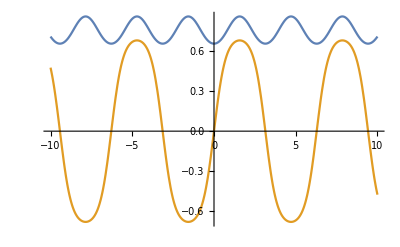

```mathematica
Plot[{
Cos@Cos@Cos@Cos@x,
Sin@Sin@Sin@Sin@x,
},{x,-10,10}]
```

```mathematica
f[x_]:=Cos@Cos@Cos@Cos@x;
g[x_]:=Sin@Sin@Sin@Sin@x;
```

```mathematica
Reduce[f[x]==g[x],x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Cos[Cos[Cos[Cos[x]]]]==Sin[Sin[Sin[Sin[x]]]],x]

```mathematica
FindInstance[f[x]==g[x],x]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

```mathematica
FindInstance[Cos[Cos[Cos[Cos[x]]]]==Sin[Sin[Sin[Sin[x]]]],x,Reals]
```

{}

```mathematica
FindRoot[f[x]==g[x],{x,ⅈ}]
```

{x→0.756887+0.610155 ⅈ}

```mathematica
Root[{f[#]-g[#]&,x/.Out[47]}]
```

Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711

```mathematica
f[Root"0.757"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.75688713734757107065576064997003413737`15.996381558333008+0.61015499692034269596518925027339719236`15.902790605814667 ⅈ}]0.7568871373475711]-g[Root"0.757"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.75688713734757107065576064997003413737`15.996381558333008+0.61015499692034269596518925027339719236`15.902790605814667 ⅈ}]0.7568871373475711]//FullSimplify
```

0

```mathematica
ComplexPlot[f[z]-g[z],{z,-1-ⅈ,1+ⅈ},PlotLegends->Automatic]
```

-Graphics-

```mathematica
NSolve[f[x]==g[x],x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[Cos[Cos[Cos[Cos[x]]]]==Sin[Sin[Sin[Sin[x]]]],x]

Cos[Cos[Cos[Cos[x]]]]==Sin[Sin[Sin[Sin[x]]]]

WolframAlphaQueryResults

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

WolframAlphaQueryResults

False

WolframAlphaQueryParseResults

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Cos[Cos[Cos[Cos[x]]]]==Sin[Sin[Sin[Sin[x]]]],x,ℂ]

WolframAlphaQueryNoResults

WolframAlphaQueryParseResults

{{x→-√3},{x→√3}}

```mathematica
LinguisticAssistant
```

{{x→-√3},{x→√3}}

FindRoot::fdss: Search specification x should be a list with 1 to 5 elements.

FindRoot[x^2-3==0,x]

```mathematica
Table[FindRoot[x^2-3==0,{x,t}],{t,-10,10}]
```

```mathematica
Table[FindRoot[f[x]==g[x],{x,RandomInteger[{-20,20}]+RandomInteger[{-20,20}]ⅈ}],{i,0,1000}]//Parallelize//DeleteDuplicates
```

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {6.-3. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {2.+3. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {7.+19. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-10.+9. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {15.-16. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-1.+10. ⅈ}.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {-12.-3. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-2.+7. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {10.-18. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.-10. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-9.+17. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-14.+8. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-19.+18. ⅈ}.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {18.+4. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-19.+8. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-18.-14. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-1.+9. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {4.+12. ⅈ}.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {-17.-4. ⅈ}.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {1.+4. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {10.-13. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-5.+20. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-12.-12. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {7.-5. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::ovfl: Overflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::ovfl: Overflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {13.+18. ⅈ}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {8.-10. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {15.-7. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {12.+12. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-4.+17. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {18.+11. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {3.-18. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-10.-5. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {2.+15. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-6.-7. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {14.-3. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-18.+10. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-10.+13. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {6.-14. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-3.+17. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-11.-12. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-2.+20. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-10.+6. ⅈ}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {-1.+3. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-2.+19. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-6.-5. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {7.+15. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-16.+6. ⅈ}.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {11.+3. ⅈ}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::ovfl: Overflow occurred in computation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-8.+5. ⅈ}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {-3.-4. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-20.-5. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {3.-11. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-20.-7. ⅈ}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-19.-9. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {6.-9. ⅈ}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {2.-12. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {9.+12. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {12.-18. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {-6.-3. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-5.+8. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {16.-8. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.+14. ⅈ}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {11.+8. ⅈ}.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {-3.+3. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-18.-6. ⅈ}.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {-14.-4. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {18.-8. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-20.+19. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.-12. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {14.-7. ⅈ}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-6.-13. ⅈ}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {16.+20. ⅈ}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-6.-19. ⅈ}.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-12.+12. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-12.-11. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {1.-15. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {15.+15. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-10.+9. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-14.-18. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-6.+19. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-10.+14. ⅈ}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-12.+14. ⅈ}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {7.-11. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {12.+14. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {3.-12. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-9.+12. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {5.-13. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {-6.+4. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-6.-14. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-18.-6. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.+5. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {19.+5. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-1.+6. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {5.-16. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {11.-7. ⅈ}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {6.-7. ⅈ}.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::ovfl: Overflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {6.+20. ⅈ}.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {16.-16. ⅈ}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {9.+20. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.-13. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {2.+6. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-4.+8. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-15.+19. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {10.-7. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {6.+7. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-14.+13. ⅈ}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-18.+13. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {10.+15. ⅈ}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-4.+13. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-11.+10. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-9.-7. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-5.-20. ⅈ}.

General::ovfl: Overflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-8.+13. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {7.+18. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {16.+12. ⅈ}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-4.+16. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-8.+5. ⅈ}.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {3.+6. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {16.+14. ⅈ}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-11.+20. ⅈ}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {16.+3. ⅈ}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-16.-7. ⅈ}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-6.+13. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{x→20.-2. ⅈ},{x→14.6902},{x→-5.26539},{x→7.30098},{x→-9.97816-1.89262 ⅈ},{x→-4.15939},{x→14.9511+0.610155 ⅈ},{x→0.-2. ⅈ},{x→1.66621+0.241886 ⅈ},{x→8.40698},{x→18.3689+1.71841 ⅈ},{x→-18.0927-0.610155 ⅈ},{x→13.5842},{x→19.6064+0.610155 ⅈ},{x→0.999655+1.99979 ⅈ},{x→0.756887+0.610155 ⅈ},{x→8.40698},{x→18.3689-1.71841 ⅈ},{x→-18.0927+0.610155 ⅈ},FindRoot[f[x]==g[x],{x,RandomInteger[{-20,20}]+RandomInteger[{-20,20}] ⅈ}],{x→-4.71011-0.0373761 ⅈ},{x→20.9734},{x→14.6902},{x→-3.-2. ⅈ},{x→-13.3065-1.36479 ⅈ},{x→-130.929},{x→-17.8318},{x→-17.9988+2.00098 ⅈ},{x→0.+2. ⅈ},{x→13.3233-0.610155 ⅈ},{x→19.6064+0.610155 ⅈ},{x→16.3051+0.862581 ⅈ},{x→10.2294+1.45339 ⅈ},{x→14.1372-1.21068 ⅈ},{x→-10.9956+1.21068 ⅈ},{x→14.9511+0.610155 ⅈ},{x→3.99932-2.00529 ⅈ},{x→15.9998+1.99826 ⅈ},{x→-12.0509+1.99038 ⅈ},{x→1.65433-0.127442 ⅈ},{x→-20.0612-0.227119 ⅈ},{x→-7.08782+1.45339 ⅈ},{x→-3.89848+0.610155 ⅈ},{x→3.-2. ⅈ},{x→13.9998-1.99967 ⅈ},{x→13.5842},{x→7.99981+2.00014 ⅈ},{x→19.6064-0.610155 ⅈ},{x→-7.0233-1.36479 ⅈ},{x→17.-2. ⅈ},{x→-16.0783+1.25988 ⅈ},{x→-5.99998-2.00002 ⅈ},{x→2.38471+0.610155 ⅈ},{x→-3.99845-2.00571 ⅈ},{x→14.9511-0.610155 ⅈ},{x→13.5842},{x→-20.+2. ⅈ},{x→0.756887-0.610155 ⅈ},{x→11.+1. ⅈ},{x→0.756887-0.610155 ⅈ},{x→-7.00273-1.99967 ⅈ},{x→-0.999655+1.99979 ⅈ},{x→-19.+2. ⅈ},{x→2.1238},{x→9.98157+1.90439 ⅈ},{x→7.85398-1.21068 ⅈ},{x→13.5842},{x→-0.999655-1.99979 ⅈ},{x→-35.5753},{x→-18.0927-0.610155 ⅈ},{x→-8.68466+1.36479 ⅈ},{x→-13.9998-1.99967 ⅈ},{x→-19.-2. ⅈ},{x→-13.9998+1.99967 ⅈ},{x→96.3716},{x→20.+2. ⅈ},{x→8.66789-0.610155 ⅈ},{x→-5.5263-0.610155 ⅈ},{x→-5.-2. ⅈ},{x→134.071},{x→-11.5486},{x→-3.99845+2.00571 ⅈ},{x→-7.08782-1.45339 ⅈ},{x→-10.4426},{x→-16.4649-0.610155 ⅈ},{x→-17.8318},{x→8.66789+0.610155 ⅈ},{x→5.-2. ⅈ},{x→7.99981-2.00014 ⅈ},{x→19.+2. ⅈ},{x→13.3233+0.610155 ⅈ},{x→2.38471-0.610155 ⅈ},{x→-5.+2. ⅈ},{x→-11.8095+0.610155 ⅈ},{x→-5.99998+2.00002 ⅈ},{x→1.0178},{x→1.66621-0.241886 ⅈ},{x→7.00272-2.00022 ⅈ},{x→3.99932+2.00529 ⅈ},{x→3.88171+1.36479 ⅈ},{x→-9.97816+1.89262 ⅈ},{x→-14.9876+1.99908 ⅈ},{x→17.9994-1.99957 ⅈ},{x→12.0531+1.98863 ⅈ},{x→-14.9876-1.99908 ⅈ},{x→-2.00001+2. ⅈ},{x→11.7617+1.45339 ⅈ},{x→1.65433+0.127442 ⅈ},{x→1.0178},{x→-17.9988-2.00098 ⅈ},{x→5.+2. ⅈ},{x→26.1505},{x→-7.00273+1.99967 ⅈ},{x→16.3051-0.862581 ⅈ},{x→10.2294-1.45339 ⅈ},{x→-10.4426},{x→14.9884+1.99798 ⅈ},{x→-13.0287+1.93553 ⅈ},{x→0.999655-1.99979 ⅈ},{x→-3.+2. ⅈ},{x→-4.15939},{x→-16.4649+0.610155 ⅈ},{x→7.04007+0.610155 ⅈ},{x→7.30098},{x→3.88171-1.36479 ⅈ},{x→-16.0783-1.25988 ⅈ},{x→-5.5263+0.610155 ⅈ},{x→3.+2. ⅈ},{x→14.9511-0.610155 ⅈ},{x→8.40698},{x→-10.1817-0.610155 ⅈ},{x→-15.9998-1.99826 ⅈ},{x→-13.0287-1.93553 ⅈ},{x→-14.9678+1.36479 ⅈ},{x→8.98248-1.99968 ⅈ},{x→-17.-2. ⅈ},{x→13.0087+1.99968 ⅈ},{x→-16.7258},{x→19.6064-0.610155 ⅈ},{x→-18.0927-0.610155 ⅈ},{x→0.756887+0.610155 ⅈ},{x→-4.71011+0.0373761 ⅈ},{x→15.9998-1.99826 ⅈ},{x→-24.1149},{x→17.9994+1.99957 ⅈ},{x→13.5842},{x→10.9983+2.00105 ⅈ},{x→14.1372+1.21068 ⅈ},{x→19.-2. ⅈ},{x→17.+2. ⅈ},{x→-8.93685-1.96907 ⅈ},{x→-3.89848-0.610155 ⅈ},{x→11.-1. ⅈ},{x→12.0531-1.98863 ⅈ},{x→-7.99981+2.00014 ⅈ},{x→-11.8095-0.610155 ⅈ},{x→-13.3065+1.36479 ⅈ},{x→-11.025-2.00287 ⅈ},{x→2.1238},{x→-10.4426},{x→9.98157-1.90439 ⅈ},{x→-17.+2. ⅈ},{x→6.00001-2.00003 ⅈ},{x→-24.1149},{x→-11.5486},{x→-7.99981-2.00014 ⅈ},{x→11.7617-1.45339 ⅈ},{x→14.9884-1.99798 ⅈ},{x→20.9734},{x→2.1238},{x→7.04007-0.610155 ⅈ},{x→-5.26539},{x→2.00001+2. ⅈ},{x→-16.7258},{x→-7.0233+1.36479 ⅈ},{x→-12.0509-1.99038 ⅈ},{x→-15.9998+1.99826 ⅈ},{x→-8.68466-1.36479 ⅈ},{x→13.9998+1.99967 ⅈ},{x→-11.5486},{x→-18.0927+0.610155 ⅈ},{x→-20.-2. ⅈ},{x→-3.89848-0.610155 ⅈ},{x→-10.9956-1.21068 ⅈ},{x→-10.1817+0.610155 ⅈ},{x→-18.0927+0.610155 ⅈ},{x→-2.00001-2. ⅈ},{x→-11.025+2.00287 ⅈ},{x→8.98248+1.99968 ⅈ},{x→10.9983-2.00105 ⅈ},{x→-8.93685+1.96907 ⅈ},{x→-11.5486},{x→13.0087-1.99968 ⅈ},{x→6.00001+2.00003 ⅈ},{x→2.00001-2. ⅈ},{x→-14.9678-1.36479 ⅈ},{x→-3.89848+0.610155 ⅈ},{x→-20.0612+0.227119 ⅈ}}

```mathematica
Catch[Module[{a},a=FindRoot[x^2-3==0,{x,0}];result[a]]]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {0.}. Try perturbing the initial point(s).

result[{x→0.}]

```mathematica
Hold[]
```

```mathematica
Hold[FindRoot[x^2-3==0,{x,0}]]
```

```mathematica
Internal`HandlerBlock[{"Message",messageHandler},(*... code here...*)]
```

```mathematica
Internal`HandlerBlock[
{"Message",Abort[]&},
FindRoot[x^2-3==0,{x,0}]
]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {0.}. Try perturbing the initial point(s).

```mathematica
r={{x->19.999995573220424-1.999999485178288 ⅈ},{x->14.69016741956822},{x->-5.265389947588615},{x->7.300981619869917},{x->-9.978157794731487-1.8926173567831734 ⅈ},{x->-4.159389606457121},{x->14.951076130601395+0.6101549969203424 ⅈ},{x->0.-1.9999999803483592 ⅈ},{x->1.6662081510339646+0.24188578236857478 ⅈ},{x->8.406981518917016},{x->18.368907003142944+1.7184064239539356 ⅈ},{x->-18.09266878419119-0.610154996920343 ⅈ},{x->13.584166474935017},{x->19.60644305888633+0.6101549969203428 ⅈ},{x->0.9996547583569015+1.9997914418884901 ⅈ},{x->0.7568871373475711+0.6101549969203427 ⅈ},{x->8.406982304344407},{x->18.368907003142944-1.7184064239539356 ⅈ},{x->-18.09266878419119+0.610154996920343 ⅈ},FindRoot[f[x]==g[x],{x,RandomInteger[{-20,20}]+RandomInteger[{-20,20}] ⅈ}],{x->-4.7101126917625855-0.03737609752108374 ⅈ},{x->20.973352649032115},{x->14.690167341913018},{x->-2.9999997999097103-1.999999560659729 ⅈ},{x->-13.3064856878961-1.3647895819066485 ⅈ},{x->-130.92909540700174},{x->-17.831759976088648},{x->-17.998845578669624+2.0009764105959995 ⅈ},{x->0.+1.9999999803483592 ⅈ},{x->13.323257751706745-0.6101549969203423 ⅈ},{x->19.60644305888633+0.6101549969203426 ⅈ},{x->16.305098663881207+0.8625807957871788 ⅈ},{x->10.229407792608843+1.4533865423612389 ⅈ},{x->14.137166941154074-1.2106840448910332 ⅈ},{x->-10.995574287564276+1.2106840448910343 ⅈ},{x->14.951076130601395+0.6101549969203425 ⅈ},{x->3.999323499651463-2.005285705040711 ⅈ},{x->15.999751999288879+1.9982568000018213 ⅈ},{x->-12.05093053224554+1.9903781501486297 ⅈ},{x->1.654329097366663-0.12744228268007746 ⅈ},{x->-20.061151609200937-0.22711919336223807 ⅈ},{x->-7.0878151390190505+1.4533865423612382 ⅈ},{x->-3.898479790937364+0.6101549969203429 ⅈ},{x->2.9999997999097103-1.999999560659729 ⅈ},{x->13.9998005799467-1.9996676303451055 ⅈ},{x->13.584166609815474},{x->7.999805135612173+2.000144180754764 ⅈ},{x->19.60644305888633-0.6101549969203426 ⅈ},{x->-7.023300380716513-1.3647895819066485 ⅈ},{x->17.000001792738473-1.9999981103778526 ⅈ},{x->-16.078269645136878+1.2598808729487738 ⅈ},{x->-5.999978660195471-2.0000218170763997 ⅈ},{x->2.384705516242222+0.6101549969203427 ⅈ},{x->-3.9984513708244385-2.005712249618282 ⅈ},{x->14.951076130601395-0.6101549969203424 ⅈ},{x->13.584166849863596},{x->-19.999995573220424+1.999999485178288 ⅈ},{x->0.756887137347571-0.6101549969203427 ⅈ},{x->11.+1. ⅈ},{x->0.7568871373475711-0.6101549969203427 ⅈ},{x->-7.002733469491642-1.9996717244608124 ⅈ},{x->-0.9996547583569015+1.9997914418884901 ⅈ},{x->-19.000000571491583+1.9999995773821853 ⅈ},{x->2.123797720271098},{x->9.981570276235251+1.9043922963348516 ⅈ},{x->7.853981633974483-1.210684044891034 ⅈ},{x->13.584166975913575},{x->-0.9996547583569015-1.9997914418884901 ⅈ},{x->-35.57531519894821},{x->-18.092668784191183-0.6101549969203428 ⅈ},{x->-8.684662887232452+1.3647895819066487 ⅈ},{x->-13.9998005799467-1.9996676303451055 ⅈ},{x->-19.000000571491583-1.9999995773821853 ⅈ},{x->-13.9998005799467+1.9996676303451055 ⅈ},{x->96.37157620834535},{x->19.999995573220424+1.999999485178288 ⅈ},{x->8.667890823421809-0.6101549969203447 ⅈ},{x->-5.526298169832016-0.6101549969203426 ⅈ},{x->-4.999999555138911-1.9999977381665728 ⅈ},{x->134.0706880144209},{x->-11.548574782168803},{x->-3.9984513708244385+2.005712249618282 ⅈ},{x->-7.0878151390190505-1.4533865423612382 ⅈ},{x->-10.442574321004207},{x->-16.464850405296538-0.6101549969203424 ⅈ},{x->-17.831760007854857},{x->8.667890823421809+0.6101549969203447 ⅈ},{x->4.999999555138911-1.9999977381665728 ⅈ},{x->7.999805135612173-2.000144180754764 ⅈ},{x->19.000000571491583+1.9999995773821853 ⅈ},{x->13.323257751706745+0.6101549969203423 ⅈ},{x->2.384705516242222-0.6101549969203427 ⅈ},{x->-4.999999555138911+1.9999977381665728 ⅈ},{x->-11.809483477011602+0.6101549969203427 ⅈ},{x->-5.999978660195471+2.0000218170763997 ⅈ},{x->1.0177973575403352},{x->1.6662081510339646-0.24188578236857478 ⅈ},{x->7.002720191942299-2.000215155285138 ⅈ},{x->3.999323499651463+2.005285705040711 ⅈ},{x->3.8817077271267206+1.3647895819066485 ⅈ},{x->-9.978157794731487+1.8926173567831734 ⅈ},{x->-14.987595321403258+1.999078790535674 ⅈ},{x->17.99942691213343-1.9995687525147086 ⅈ},{x->12.053085884082357+1.9886328493118033 ⅈ},{x->-14.987595321403258-1.999078790535674 ⅈ},{x->-2.000005056204302+2.0000017911640895 ⅈ},{x->11.761740782519704+1.4533865423611478 ⅈ},{x->1.654329097366663+0.12744228268007746 ⅈ},{x->1.0177971572920723},{x->-17.998845578669624-2.0009764105959995 ⅈ},{x->4.999999555138911+1.9999977381665728 ⅈ},{x->26.150537228071833},{x->-7.002733469491642+1.9996717244608124 ⅈ},{x->16.305098663881207-0.8625807957871788 ⅈ},{x->10.229407792608843-1.4533865423612389 ⅈ},{x->-10.442574111215466},{x->14.988379627249847+1.9979825628146888 ⅈ},{x->-13.028654758316542+1.9355341257201717 ⅈ},{x->0.9996547583569015-1.9997914418884901 ⅈ},{x->-2.9999997999097103+1.999999560659729 ⅈ},{x->-4.159388226757861},{x->-16.464850405296538+0.6101549969203424 ⅈ},{x->7.040072444527158+0.6101549969203423 ⅈ},{x->7.300981036896941},{x->3.8817077271267206-1.3647895819066485 ⅈ},{x->-16.078269645136878-1.2598808729487738 ⅈ},{x->-5.526298169832016+0.6101549969203426 ⅈ},{x->2.9999997999097103+1.999999560659729 ⅈ},{x->14.951076130601395-0.6101549969203425 ⅈ},{x->8.406981647737156},{x->-10.18166509811695-0.6101549969203414 ⅈ},{x->-15.999751999406838-1.9982567998092637 ⅈ},{x->-13.028654758316542-1.9355341257201717 ⅈ},{x->-14.967848194412039+1.3647895819066485 ⅈ},{x->8.982483424394207-1.9996800314748364 ⅈ},{x->-17.000001792738473-1.9999981103778526 ⅈ},{x->13.008665150734346+1.9996800314748362 ⅈ},{x->-16.725759105250447},{x->19.60644305888633-0.6101549969203428 ⅈ},{x->-18.09266878419119-0.6101549969203424 ⅈ},{x->0.756887137347571+0.6101549969203427 ⅈ},{x->-4.7101126917625855+0.03737609752108374 ⅈ},{x->15.999751999288879-1.9982568000018213 ⅈ},{x->-24.114945209033138},{x->17.99942691213343+1.9995687525147086 ⅈ},{x->13.584166954890986},{x->10.99834857946081+2.0010533304652043 ⅈ},{x->14.137166941154074+1.2106840448910332 ⅈ},{x->19.000000571491583-1.9999995773821853 ⅈ},{x->17.000001792738473+1.9999981103778526 ⅈ},{x->-8.936853913700487-1.9690670294883736 ⅈ},{x->-3.898479790937364-0.6101549969203429 ⅈ},{x->11.-1. ⅈ},{x->12.053085884082357-1.9886328493118033 ⅈ},{x->-7.999805135612173+2.000144180754764 ⅈ},{x->-11.809483477011602-0.6101549969203427 ⅈ},{x->-13.3064856878961+1.3647895819066485 ⅈ},{x->-11.025030738977645-2.002865097158896 ⅈ},{x->2.123795879458839},{x->-10.442573725355258},{x->9.981570276235251-1.9043922963348516 ⅈ},{x->-17.000001792738473+1.9999981103778526 ⅈ},{x->6.000009882844184-2.0000296962153703 ⅈ},{x->-24.11494508547603},{x->-11.548574377076873},{x->-7.999805135612173-2.000144180754764 ⅈ},{x->11.761740782519704-1.4533865423611478 ⅈ},{x->14.988379627249847-1.9979825628146888 ⅈ},{x->20.973352688234925},{x->2.1237952652849827},{x->7.040072444527158-0.6101549969203423 ⅈ},{x->-5.2653890455983365},{x->2.000005056204302+2.0000017911640895 ⅈ},{x->-16.725759326178373},{x->-7.023300380716513+1.3647895819066485 ⅈ},{x->-12.05093053224554-1.9903781501486297 ⅈ},{x->-15.999751999406838+1.9982567998092637 ⅈ},{x->-8.684662887232452-1.3647895819066487 ⅈ},{x->13.9998005799467+1.9996676303451055 ⅈ},{x->-11.548574490091452},{x->-18.092668784191183+0.6101549969203428 ⅈ},{x->-19.999995573220424-1.999999485178288 ⅈ},{x->-3.898479790937364-0.6101549969203425 ⅈ},{x->-10.995574287564276-1.2106840448910343 ⅈ},{x->-10.18166509811695+0.6101549969203414 ⅈ},{x->-18.09266878419119+0.6101549969203424 ⅈ},{x->-2.000005056204302-2.0000017911640895 ⅈ},{x->-11.025030738977645+2.002865097158896 ⅈ},{x->8.982483424394207+1.9996800314748364 ⅈ},{x->10.99834857946081-2.0010533304652043 ⅈ},{x->-8.936853913700487+1.9690670294883736 ⅈ},{x->-11.548574262834343},{x->13.008665150734346-1.9996800314748362 ⅈ},{x->6.000009882844184+2.0000296962153703 ⅈ},{x->2.000005056204302-2.0000017911640895 ⅈ},{x->-14.967848194412039-1.3647895819066485 ⅈ},{x->-3.898479790937364+0.6101549969203425 ⅈ},{x->-20.061151609200937+0.22711919336223807 ⅈ}};
```

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {-19.-19. ⅈ}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {8.-7. ⅈ}.

```mathematica
r=x/.r
```

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {12.+10. ⅈ}.

ReplaceAll::rmix: Elements of {{x→20.-2. ⅈ},{x→14.6902},{x→-5.26539},{x→7.30098},{x→-9.97816-1.89262 ⅈ},{x→-«18»},{x→14.9511+0.610155 ⅈ},{x→0.-2. ⅈ},{x→1.66621+0.241886 ⅈ},{x→8.40698},«188»} are a mixture of lists and nonlists.

{20.-2. ⅈ,14.6902,-5.26539,7.30098,-9.97816-1.89262 ⅈ,-4.15939,14.9511+0.610155 ⅈ,0.-2. ⅈ,1.66621+0.241886 ⅈ,8.40698,18.3689+1.71841 ⅈ,-18.0927-0.610155 ⅈ,13.5842,19.6064+0.610155 ⅈ,0.999655+1.99979 ⅈ,0.756887+0.610155 ⅈ,8.40698,18.3689-1.71841 ⅈ,-18.0927+0.610155 ⅈ,-8.93685-1.96907 ⅈ,-4.71011-0.0373761 ⅈ,20.9734,14.6902,-3.-2. ⅈ,-13.3065-1.36479 ⅈ,-130.929,-17.8318,-17.9988+2.00098 ⅈ,0.+2. ⅈ,13.3233-0.610155 ⅈ,19.6064+0.610155 ⅈ,16.3051+0.862581 ⅈ,10.2294+1.45339 ⅈ,14.1372-1.21068 ⅈ,-10.9956+1.21068 ⅈ,14.9511+0.610155 ⅈ,3.99932-2.00529 ⅈ,15.9998+1.99826 ⅈ,-12.0509+1.99038 ⅈ,1.65433-0.127442 ⅈ,-20.0612-0.227119 ⅈ,-7.08782+1.45339 ⅈ,-3.89848+0.610155 ⅈ,3.-2. ⅈ,13.9998-1.99967 ⅈ,13.5842,7.99981+2.00014 ⅈ,19.6064-0.610155 ⅈ,-7.0233-1.36479 ⅈ,17.-2. ⅈ,-16.0783+1.25988 ⅈ,-5.99998-2.00002 ⅈ,2.38471+0.610155 ⅈ,-3.99845-2.00571 ⅈ,14.9511-0.610155 ⅈ,13.5842,-20.+2. ⅈ,0.756887-0.610155 ⅈ,11.+1. ⅈ,0.756887-0.610155 ⅈ,-7.00273-1.99967 ⅈ,-0.999655+1.99979 ⅈ,-19.+2. ⅈ,2.1238,9.98157+1.90439 ⅈ,7.85398-1.21068 ⅈ,13.5842,-0.999655-1.99979 ⅈ,-35.5753,-18.0927-0.610155 ⅈ,-8.68466+1.36479 ⅈ,-13.9998-1.99967 ⅈ,-19.-2. ⅈ,-13.9998+1.99967 ⅈ,96.3716,20.+2. ⅈ,8.66789-0.610155 ⅈ,-5.5263-0.610155 ⅈ,-5.-2. ⅈ,134.071,-11.5486,-3.99845+2.00571 ⅈ,-7.08782-1.45339 ⅈ,-10.4426,-16.4649-0.610155 ⅈ,-17.8318,8.66789+0.610155 ⅈ,5.-2. ⅈ,7.99981-2.00014 ⅈ,19.+2. ⅈ,13.3233+0.610155 ⅈ,2.38471-0.610155 ⅈ,-5.+2. ⅈ,-11.8095+0.610155 ⅈ,-5.99998+2.00002 ⅈ,1.0178,1.66621-0.241886 ⅈ,7.00272-2.00022 ⅈ,3.99932+2.00529 ⅈ,3.88171+1.36479 ⅈ,-9.97816+1.89262 ⅈ,-14.9876+1.99908 ⅈ,17.9994-1.99957 ⅈ,12.0531+1.98863 ⅈ,-14.9876-1.99908 ⅈ,-2.00001+2. ⅈ,11.7617+1.45339 ⅈ,1.65433+0.127442 ⅈ,1.0178,-17.9988-2.00098 ⅈ,5.+2. ⅈ,26.1505,-7.00273+1.99967 ⅈ,16.3051-0.862581 ⅈ,10.2294-1.45339 ⅈ,-10.4426,14.9884+1.99798 ⅈ,-13.0287+1.93553 ⅈ,0.999655-1.99979 ⅈ,-3.+2. ⅈ,-4.15939,-16.4649+0.610155 ⅈ,7.04007+0.610155 ⅈ,7.30098,3.88171-1.36479 ⅈ,-16.0783-1.25988 ⅈ,-5.5263+0.610155 ⅈ,3.+2. ⅈ,14.9511-0.610155 ⅈ,8.40698,-10.1817-0.610155 ⅈ,-15.9998-1.99826 ⅈ,-13.0287-1.93553 ⅈ,-14.9678+1.36479 ⅈ,8.98248-1.99968 ⅈ,-17.-2. ⅈ,13.0087+1.99968 ⅈ,-16.7258,19.6064-0.610155 ⅈ,-18.0927-0.610155 ⅈ,0.756887+0.610155 ⅈ,-4.71011+0.0373761 ⅈ,15.9998-1.99826 ⅈ,-24.1149,17.9994+1.99957 ⅈ,13.5842,10.9983+2.00105 ⅈ,14.1372+1.21068 ⅈ,19.-2. ⅈ,17.+2. ⅈ,-8.93685-1.96907 ⅈ,-3.89848-0.610155 ⅈ,11.-1. ⅈ,12.0531-1.98863 ⅈ,-7.99981+2.00014 ⅈ,-11.8095-0.610155 ⅈ,-13.3065+1.36479 ⅈ,-11.025-2.00287 ⅈ,2.1238,-10.4426,9.98157-1.90439 ⅈ,-17.+2. ⅈ,6.00001-2.00003 ⅈ,-24.1149,-11.5486,-7.99981-2.00014 ⅈ,11.7617-1.45339 ⅈ,14.9884-1.99798 ⅈ,20.9734,2.1238,7.04007-0.610155 ⅈ,-5.26539,2.00001+2. ⅈ,-16.7258,-7.0233+1.36479 ⅈ,-12.0509-1.99038 ⅈ,-15.9998+1.99826 ⅈ,-8.68466-1.36479 ⅈ,13.9998+1.99967 ⅈ,-11.5486,-18.0927+0.610155 ⅈ,-20.-2. ⅈ,-3.89848-0.610155 ⅈ,-10.9956-1.21068 ⅈ,-10.1817+0.610155 ⅈ,-18.0927+0.610155 ⅈ,-2.00001-2. ⅈ,-11.025+2.00287 ⅈ,8.98248+1.99968 ⅈ,10.9983-2.00105 ⅈ,-8.93685+1.96907 ⅈ,-11.5486,13.0087-1.99968 ⅈ,6.00001+2.00003 ⅈ,2.00001-2. ⅈ,-14.9678-1.36479 ⅈ,-3.89848+0.610155 ⅈ,-20.0612+0.227119 ⅈ}

```mathematica
r
```

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x} = {-4.-3. ⅈ}.

ReplaceAll::rmix: Elements of {{x→20.-2. ⅈ},{x→14.6902},{x→-5.26539},{x→7.30098},{x→-9.97816-1.89262 ⅈ},{x→-«18»},{x→14.9511+0.610155 ⅈ},{x→0.-2. ⅈ},{x→1.66621+0.241886 ⅈ},{x→8.40698},«188»} are a mixture of lists and nonlists.

x/.{{x→20.-2. ⅈ},{x→14.6902},{x→-5.26539},{x→7.30098},{x→-9.97816-1.89262 ⅈ},{x→-4.15939},{x→14.9511+0.610155 ⅈ},{x→0.-2. ⅈ},{x→1.66621+0.241886 ⅈ},{x→8.40698},{x→18.3689+1.71841 ⅈ},{x→-18.0927-0.610155 ⅈ},{x→13.5842},{x→19.6064+0.610155 ⅈ},{x→0.999655+1.99979 ⅈ},{x→0.756887+0.610155 ⅈ},{x→8.40698},{x→18.3689-1.71841 ⅈ},{x→-18.0927+0.610155 ⅈ},FindRoot[f[x]==g[x],{x,RandomInteger[{-20,20}]+RandomInteger[{-20,20}] ⅈ}],{x→-4.71011-0.0373761 ⅈ},{x→20.9734},{x→14.6902},{x→-3.-2. ⅈ},{x→-13.3065-1.36479 ⅈ},{x→-130.929},{x→-17.8318},{x→-17.9988+2.00098 ⅈ},{x→0.+2. ⅈ},{x→13.3233-0.610155 ⅈ},{x→19.6064+0.610155 ⅈ},{x→16.3051+0.862581 ⅈ},{x→10.2294+1.45339 ⅈ},{x→14.1372-1.21068 ⅈ},{x→-10.9956+1.21068 ⅈ},{x→14.9511+0.610155 ⅈ},{x→3.99932-2.00529 ⅈ},{x→15.9998+1.99826 ⅈ},{x→-12.0509+1.99038 ⅈ},{x→1.65433-0.127442 ⅈ},{x→-20.0612-0.227119 ⅈ},{x→-7.08782+1.45339 ⅈ},{x→-3.89848+0.610155 ⅈ},{x→3.-2. ⅈ},{x→13.9998-1.99967 ⅈ},{x→13.5842},{x→7.99981+2.00014 ⅈ},{x→19.6064-0.610155 ⅈ},{x→-7.0233-1.36479 ⅈ},{x→17.-2. ⅈ},{x→-16.0783+1.25988 ⅈ},{x→-5.99998-2.00002 ⅈ},{x→2.38471+0.610155 ⅈ},{x→-3.99845-2.00571 ⅈ},{x→14.9511-0.610155 ⅈ},{x→13.5842},{x→-20.+2. ⅈ},{x→0.756887-0.610155 ⅈ},{x→11.+1. ⅈ},{x→0.756887-0.610155 ⅈ},{x→-7.00273-1.99967 ⅈ},{x→-0.999655+1.99979 ⅈ},{x→-19.+2. ⅈ},{x→2.1238},{x→9.98157+1.90439 ⅈ},{x→7.85398-1.21068 ⅈ},{x→13.5842},{x→-0.999655-1.99979 ⅈ},{x→-35.5753},{x→-18.0927-0.610155 ⅈ},{x→-8.68466+1.36479 ⅈ},{x→-13.9998-1.99967 ⅈ},{x→-19.-2. ⅈ},{x→-13.9998+1.99967 ⅈ},{x→96.3716},{x→20.+2. ⅈ},{x→8.66789-0.610155 ⅈ},{x→-5.5263-0.610155 ⅈ},{x→-5.-2. ⅈ},{x→134.071},{x→-11.5486},{x→-3.99845+2.00571 ⅈ},{x→-7.08782-1.45339 ⅈ},{x→-10.4426},{x→-16.4649-0.610155 ⅈ},{x→-17.8318},{x→8.66789+0.610155 ⅈ},{x→5.-2. ⅈ},{x→7.99981-2.00014 ⅈ},{x→19.+2. ⅈ},{x→13.3233+0.610155 ⅈ},{x→2.38471-0.610155 ⅈ},{x→-5.+2. ⅈ},{x→-11.8095+0.610155 ⅈ},{x→-5.99998+2.00002 ⅈ},{x→1.0178},{x→1.66621-0.241886 ⅈ},{x→7.00272-2.00022 ⅈ},{x→3.99932+2.00529 ⅈ},{x→3.88171+1.36479 ⅈ},{x→-9.97816+1.89262 ⅈ},{x→-14.9876+1.99908 ⅈ},{x→17.9994-1.99957 ⅈ},{x→12.0531+1.98863 ⅈ},{x→-14.9876-1.99908 ⅈ},{x→-2.00001+2. ⅈ},{x→11.7617+1.45339 ⅈ},{x→1.65433+0.127442 ⅈ},{x→1.0178},{x→-17.9988-2.00098 ⅈ},{x→5.+2. ⅈ},{x→26.1505},{x→-7.00273+1.99967 ⅈ},{x→16.3051-0.862581 ⅈ},{x→10.2294-1.45339 ⅈ},{x→-10.4426},{x→14.9884+1.99798 ⅈ},{x→-13.0287+1.93553 ⅈ},{x→0.999655-1.99979 ⅈ},{x→-3.+2. ⅈ},{x→-4.15939},{x→-16.4649+0.610155 ⅈ},{x→7.04007+0.610155 ⅈ},{x→7.30098},{x→3.88171-1.36479 ⅈ},{x→-16.0783-1.25988 ⅈ},{x→-5.5263+0.610155 ⅈ},{x→3.+2. ⅈ},{x→14.9511-0.610155 ⅈ},{x→8.40698},{x→-10.1817-0.610155 ⅈ},{x→-15.9998-1.99826 ⅈ},{x→-13.0287-1.93553 ⅈ},{x→-14.9678+1.36479 ⅈ},{x→8.98248-1.99968 ⅈ},{x→-17.-2. ⅈ},{x→13.0087+1.99968 ⅈ},{x→-16.7258},{x→19.6064-0.610155 ⅈ},{x→-18.0927-0.610155 ⅈ},{x→0.756887+0.610155 ⅈ},{x→-4.71011+0.0373761 ⅈ},{x→15.9998-1.99826 ⅈ},{x→-24.1149},{x→17.9994+1.99957 ⅈ},{x→13.5842},{x→10.9983+2.00105 ⅈ},{x→14.1372+1.21068 ⅈ},{x→19.-2. ⅈ},{x→17.+2. ⅈ},{x→-8.93685-1.96907 ⅈ},{x→-3.89848-0.610155 ⅈ},{x→11.-1. ⅈ},{x→12.0531-1.98863 ⅈ},{x→-7.99981+2.00014 ⅈ},{x→-11.8095-0.610155 ⅈ},{x→-13.3065+1.36479 ⅈ},{x→-11.025-2.00287 ⅈ},{x→2.1238},{x→-10.4426},{x→9.98157-1.90439 ⅈ},{x→-17.+2. ⅈ},{x→6.00001-2.00003 ⅈ},{x→-24.1149},{x→-11.5486},{x→-7.99981-2.00014 ⅈ},{x→11.7617-1.45339 ⅈ},{x→14.9884-1.99798 ⅈ},{x→20.9734},{x→2.1238},{x→7.04007-0.610155 ⅈ},{x→-5.26539},{x→2.00001+2. ⅈ},{x→-16.7258},{x→-7.0233+1.36479 ⅈ},{x→-12.0509-1.99038 ⅈ},{x→-15.9998+1.99826 ⅈ},{x→-8.68466-1.36479 ⅈ},{x→13.9998+1.99967 ⅈ},{x→-11.5486},{x→-18.0927+0.610155 ⅈ},{x→-20.-2. ⅈ},{x→-3.89848-0.610155 ⅈ},{x→-10.9956-1.21068 ⅈ},{x→-10.1817+0.610155 ⅈ},{x→-18.0927+0.610155 ⅈ},{x→-2.00001-2. ⅈ},{x→-11.025+2.00287 ⅈ},{x→8.98248+1.99968 ⅈ},{x→10.9983-2.00105 ⅈ},{x→-8.93685+1.96907 ⅈ},{x→-11.5486},{x→13.0087-1.99968 ⅈ},{x→6.00001+2.00003 ⅈ},{x→2.00001-2. ⅈ},{x→-14.9678-1.36479 ⅈ},{x→-3.89848+0.610155 ⅈ},{x→-20.0612+0.227119 ⅈ}}

```mathematica
r={19.999995573220424-1.999999485178288 ⅈ,14.69016741956822,-5.265389947588615,7.300981619869917,-9.978157794731487-1.8926173567831734 ⅈ,-4.159389606457121,14.951076130601395+0.6101549969203424 ⅈ,0.-1.9999999803483592 ⅈ,1.6662081510339646+0.24188578236857478 ⅈ,8.406981518917016,18.368907003142944+1.7184064239539356 ⅈ,-18.09266878419119-0.610154996920343 ⅈ,13.584166474935017,19.60644305888633+0.6101549969203428 ⅈ,0.9996547583569015+1.9997914418884901 ⅈ,0.7568871373475711+0.6101549969203427 ⅈ,8.406982304344407,18.368907003142944-1.7184064239539356 ⅈ,-18.09266878419119+0.610154996920343 ⅈ,-8.936853913700487-1.9690670294883736 ⅈ,-4.7101126917625855-0.03737609752108374 ⅈ,20.973352649032115,14.690167341913018,-2.9999997999097103-1.999999560659729 ⅈ,-13.3064856878961-1.3647895819066485 ⅈ,-130.92909540700174,-17.831759976088648,-17.998845578669624+2.0009764105959995 ⅈ,0.+1.9999999803483592 ⅈ,13.323257751706745-0.6101549969203423 ⅈ,19.60644305888633+0.6101549969203426 ⅈ,16.305098663881207+0.8625807957871788 ⅈ,10.229407792608843+1.4533865423612389 ⅈ,14.137166941154074-1.2106840448910332 ⅈ,-10.995574287564276+1.2106840448910343 ⅈ,14.951076130601395+0.6101549969203425 ⅈ,3.999323499651463-2.005285705040711 ⅈ,15.999751999288879+1.9982568000018213 ⅈ,-12.05093053224554+1.9903781501486297 ⅈ,1.654329097366663-0.12744228268007746 ⅈ,-20.061151609200937-0.22711919336223807 ⅈ,-7.0878151390190505+1.4533865423612382 ⅈ,-3.898479790937364+0.6101549969203429 ⅈ,2.9999997999097103-1.999999560659729 ⅈ,13.9998005799467-1.9996676303451055 ⅈ,13.584166609815474,7.999805135612173+2.000144180754764 ⅈ,19.60644305888633-0.6101549969203426 ⅈ,-7.023300380716513-1.3647895819066485 ⅈ,17.000001792738473-1.9999981103778526 ⅈ,-16.078269645136878+1.2598808729487738 ⅈ,-5.999978660195471-2.0000218170763997 ⅈ,2.384705516242222+0.6101549969203427 ⅈ,-3.9984513708244385-2.005712249618282 ⅈ,14.951076130601395-0.6101549969203424 ⅈ,13.584166849863596,-19.999995573220424+1.999999485178288 ⅈ,0.756887137347571-0.6101549969203427 ⅈ,11.+1. ⅈ,0.7568871373475711-0.6101549969203427 ⅈ,-7.002733469491642-1.9996717244608124 ⅈ,-0.9996547583569015+1.9997914418884901 ⅈ,-19.000000571491583+1.9999995773821853 ⅈ,2.123797720271098,9.981570276235251+1.9043922963348516 ⅈ,7.853981633974483-1.210684044891034 ⅈ,13.584166975913575,-0.9996547583569015-1.9997914418884901 ⅈ,-35.57531519894821,-18.092668784191183-0.6101549969203428 ⅈ,-8.684662887232452+1.3647895819066487 ⅈ,-13.9998005799467-1.9996676303451055 ⅈ,-19.000000571491583-1.9999995773821853 ⅈ,-13.9998005799467+1.9996676303451055 ⅈ,96.37157620834535,19.999995573220424+1.999999485178288 ⅈ,8.667890823421809-0.6101549969203447 ⅈ,-5.526298169832016-0.6101549969203426 ⅈ,-4.999999555138911-1.9999977381665728 ⅈ,134.0706880144209,-11.548574782168803,-3.9984513708244385+2.005712249618282 ⅈ,-7.0878151390190505-1.4533865423612382 ⅈ,-10.442574321004207,-16.464850405296538-0.6101549969203424 ⅈ,-17.831760007854857,8.667890823421809+0.6101549969203447 ⅈ,4.999999555138911-1.9999977381665728 ⅈ,7.999805135612173-2.000144180754764 ⅈ,19.000000571491583+1.9999995773821853 ⅈ,13.323257751706745+0.6101549969203423 ⅈ,2.384705516242222-0.6101549969203427 ⅈ,-4.999999555138911+1.9999977381665728 ⅈ,-11.809483477011602+0.6101549969203427 ⅈ,-5.999978660195471+2.0000218170763997 ⅈ,1.0177973575403352,1.6662081510339646-0.24188578236857478 ⅈ,7.002720191942299-2.000215155285138 ⅈ,3.999323499651463+2.005285705040711 ⅈ,3.8817077271267206+1.3647895819066485 ⅈ,-9.978157794731487+1.8926173567831734 ⅈ,-14.987595321403258+1.999078790535674 ⅈ,17.99942691213343-1.9995687525147086 ⅈ,12.053085884082357+1.9886328493118033 ⅈ,-14.987595321403258-1.999078790535674 ⅈ,-2.000005056204302+2.0000017911640895 ⅈ,11.761740782519704+1.4533865423611478 ⅈ,1.654329097366663+0.12744228268007746 ⅈ,1.0177971572920723,-17.998845578669624-2.0009764105959995 ⅈ,4.999999555138911+1.9999977381665728 ⅈ,26.150537228071833,-7.002733469491642+1.9996717244608124 ⅈ,16.305098663881207-0.8625807957871788 ⅈ,10.229407792608843-1.4533865423612389 ⅈ,-10.442574111215466,14.988379627249847+1.9979825628146888 ⅈ,-13.028654758316542+1.9355341257201717 ⅈ,0.9996547583569015-1.9997914418884901 ⅈ,-2.9999997999097103+1.999999560659729 ⅈ,-4.159388226757861,-16.464850405296538+0.6101549969203424 ⅈ,7.040072444527158+0.6101549969203423 ⅈ,7.300981036896941,3.8817077271267206-1.3647895819066485 ⅈ,-16.078269645136878-1.2598808729487738 ⅈ,-5.526298169832016+0.6101549969203426 ⅈ,2.9999997999097103+1.999999560659729 ⅈ,14.951076130601395-0.6101549969203425 ⅈ,8.406981647737156,-10.18166509811695-0.6101549969203414 ⅈ,-15.999751999406838-1.9982567998092637 ⅈ,-13.028654758316542-1.9355341257201717 ⅈ,-14.967848194412039+1.3647895819066485 ⅈ,8.982483424394207-1.9996800314748364 ⅈ,-17.000001792738473-1.9999981103778526 ⅈ,13.008665150734346+1.9996800314748362 ⅈ,-16.725759105250447,19.60644305888633-0.6101549969203428 ⅈ,-18.09266878419119-0.6101549969203424 ⅈ,0.756887137347571+0.6101549969203427 ⅈ,-4.7101126917625855+0.03737609752108374 ⅈ,15.999751999288879-1.9982568000018213 ⅈ,-24.114945209033138,17.99942691213343+1.9995687525147086 ⅈ,13.584166954890986,10.99834857946081+2.0010533304652043 ⅈ,14.137166941154074+1.2106840448910332 ⅈ,19.000000571491583-1.9999995773821853 ⅈ,17.000001792738473+1.9999981103778526 ⅈ,-8.936853913700487-1.9690670294883736 ⅈ,-3.898479790937364-0.6101549969203429 ⅈ,11.-1. ⅈ,12.053085884082357-1.9886328493118033 ⅈ,-7.999805135612173+2.000144180754764 ⅈ,-11.809483477011602-0.6101549969203427 ⅈ,-13.3064856878961+1.3647895819066485 ⅈ,-11.025030738977645-2.002865097158896 ⅈ,2.123795879458839,-10.442573725355258,9.981570276235251-1.9043922963348516 ⅈ,-17.000001792738473+1.9999981103778526 ⅈ,6.000009882844184-2.0000296962153703 ⅈ,-24.11494508547603,-11.548574377076873,-7.999805135612173-2.000144180754764 ⅈ,11.761740782519704-1.4533865423611478 ⅈ,14.988379627249847-1.9979825628146888 ⅈ,20.973352688234925,2.1237952652849827,7.040072444527158-0.6101549969203423 ⅈ,-5.2653890455983365,2.000005056204302+2.0000017911640895 ⅈ,-16.725759326178373,-7.023300380716513+1.3647895819066485 ⅈ,-12.05093053224554-1.9903781501486297 ⅈ,-15.999751999406838+1.9982567998092637 ⅈ,-8.684662887232452-1.3647895819066487 ⅈ,13.9998005799467+1.9996676303451055 ⅈ,-11.548574490091452,-18.092668784191183+0.6101549969203428 ⅈ,-19.999995573220424-1.999999485178288 ⅈ,-3.898479790937364-0.6101549969203425 ⅈ,-10.995574287564276-1.2106840448910343 ⅈ,-10.18166509811695+0.6101549969203414 ⅈ,-18.09266878419119+0.6101549969203424 ⅈ,-2.000005056204302-2.0000017911640895 ⅈ,-11.025030738977645+2.002865097158896 ⅈ,8.982483424394207+1.9996800314748364 ⅈ,10.99834857946081-2.0010533304652043 ⅈ,-8.936853913700487+1.9690670294883736 ⅈ,-11.548574262834343,13.008665150734346-1.9996800314748362 ⅈ,6.000009882844184+2.0000296962153703 ⅈ,2.000005056204302-2.0000017911640895 ⅈ,-14.967848194412039-1.3647895819066485 ⅈ,-3.898479790937364+0.6101549969203425 ⅈ,-20.061151609200937+0.22711919336223807 ⅈ}
```

{20.-2. ⅈ,14.6902,-5.26539,7.30098,-9.97816-1.89262 ⅈ,-4.15939,14.9511+0.610155 ⅈ,0.-2. ⅈ,1.66621+0.241886 ⅈ,8.40698,18.3689+1.71841 ⅈ,-18.0927-0.610155 ⅈ,13.5842,19.6064+0.610155 ⅈ,0.999655+1.99979 ⅈ,0.756887+0.610155 ⅈ,8.40698,18.3689-1.71841 ⅈ,-18.0927+0.610155 ⅈ,-8.93685-1.96907 ⅈ,-4.71011-0.0373761 ⅈ,20.9734,14.6902,-3.-2. ⅈ,-13.3065-1.36479 ⅈ,-130.929,-17.8318,-17.9988+2.00098 ⅈ,0.+2. ⅈ,13.3233-0.610155 ⅈ,19.6064+0.610155 ⅈ,16.3051+0.862581 ⅈ,10.2294+1.45339 ⅈ,14.1372-1.21068 ⅈ,-10.9956+1.21068 ⅈ,14.9511+0.610155 ⅈ,3.99932-2.00529 ⅈ,15.9998+1.99826 ⅈ,-12.0509+1.99038 ⅈ,1.65433-0.127442 ⅈ,-20.0612-0.227119 ⅈ,-7.08782+1.45339 ⅈ,-3.89848+0.610155 ⅈ,3.-2. ⅈ,13.9998-1.99967 ⅈ,13.5842,7.99981+2.00014 ⅈ,19.6064-0.610155 ⅈ,-7.0233-1.36479 ⅈ,17.-2. ⅈ,-16.0783+1.25988 ⅈ,-5.99998-2.00002 ⅈ,2.38471+0.610155 ⅈ,-3.99845-2.00571 ⅈ,14.9511-0.610155 ⅈ,13.5842,-20.+2. ⅈ,0.756887-0.610155 ⅈ,11.+1. ⅈ,0.756887-0.610155 ⅈ,-7.00273-1.99967 ⅈ,-0.999655+1.99979 ⅈ,-19.+2. ⅈ,2.1238,9.98157+1.90439 ⅈ,7.85398-1.21068 ⅈ,13.5842,-0.999655-1.99979 ⅈ,-35.5753,-18.0927-0.610155 ⅈ,-8.68466+1.36479 ⅈ,-13.9998-1.99967 ⅈ,-19.-2. ⅈ,-13.9998+1.99967 ⅈ,96.3716,20.+2. ⅈ,8.66789-0.610155 ⅈ,-5.5263-0.610155 ⅈ,-5.-2. ⅈ,134.071,-11.5486,-3.99845+2.00571 ⅈ,-7.08782-1.45339 ⅈ,-10.4426,-16.4649-0.610155 ⅈ,-17.8318,8.66789+0.610155 ⅈ,5.-2. ⅈ,7.99981-2.00014 ⅈ,19.+2. ⅈ,13.3233+0.610155 ⅈ,2.38471-0.610155 ⅈ,-5.+2. ⅈ,-11.8095+0.610155 ⅈ,-5.99998+2.00002 ⅈ,1.0178,1.66621-0.241886 ⅈ,7.00272-2.00022 ⅈ,3.99932+2.00529 ⅈ,3.88171+1.36479 ⅈ,-9.97816+1.89262 ⅈ,-14.9876+1.99908 ⅈ,17.9994-1.99957 ⅈ,12.0531+1.98863 ⅈ,-14.9876-1.99908 ⅈ,-2.00001+2. ⅈ,11.7617+1.45339 ⅈ,1.65433+0.127442 ⅈ,1.0178,-17.9988-2.00098 ⅈ,5.+2. ⅈ,26.1505,-7.00273+1.99967 ⅈ,16.3051-0.862581 ⅈ,10.2294-1.45339 ⅈ,-10.4426,14.9884+1.99798 ⅈ,-13.0287+1.93553 ⅈ,0.999655-1.99979 ⅈ,-3.+2. ⅈ,-4.15939,-16.4649+0.610155 ⅈ,7.04007+0.610155 ⅈ,7.30098,3.88171-1.36479 ⅈ,-16.0783-1.25988 ⅈ,-5.5263+0.610155 ⅈ,3.+2. ⅈ,14.9511-0.610155 ⅈ,8.40698,-10.1817-0.610155 ⅈ,-15.9998-1.99826 ⅈ,-13.0287-1.93553 ⅈ,-14.9678+1.36479 ⅈ,8.98248-1.99968 ⅈ,-17.-2. ⅈ,13.0087+1.99968 ⅈ,-16.7258,19.6064-0.610155 ⅈ,-18.0927-0.610155 ⅈ,0.756887+0.610155 ⅈ,-4.71011+0.0373761 ⅈ,15.9998-1.99826 ⅈ,-24.1149,17.9994+1.99957 ⅈ,13.5842,10.9983+2.00105 ⅈ,14.1372+1.21068 ⅈ,19.-2. ⅈ,17.+2. ⅈ,-8.93685-1.96907 ⅈ,-3.89848-0.610155 ⅈ,11.-1. ⅈ,12.0531-1.98863 ⅈ,-7.99981+2.00014 ⅈ,-11.8095-0.610155 ⅈ,-13.3065+1.36479 ⅈ,-11.025-2.00287 ⅈ,2.1238,-10.4426,9.98157-1.90439 ⅈ,-17.+2. ⅈ,6.00001-2.00003 ⅈ,-24.1149,-11.5486,-7.99981-2.00014 ⅈ,11.7617-1.45339 ⅈ,14.9884-1.99798 ⅈ,20.9734,2.1238,7.04007-0.610155 ⅈ,-5.26539,2.00001+2. ⅈ,-16.7258,-7.0233+1.36479 ⅈ,-12.0509-1.99038 ⅈ,-15.9998+1.99826 ⅈ,-8.68466-1.36479 ⅈ,13.9998+1.99967 ⅈ,-11.5486,-18.0927+0.610155 ⅈ,-20.-2. ⅈ,-3.89848-0.610155 ⅈ,-10.9956-1.21068 ⅈ,-10.1817+0.610155 ⅈ,-18.0927+0.610155 ⅈ,-2.00001-2. ⅈ,-11.025+2.00287 ⅈ,8.98248+1.99968 ⅈ,10.9983-2.00105 ⅈ,-8.93685+1.96907 ⅈ,-11.5486,13.0087-1.99968 ⅈ,6.00001+2.00003 ⅈ,2.00001-2. ⅈ,-14.9678-1.36479 ⅈ,-3.89848+0.610155 ⅈ,-20.0612+0.227119 ⅈ}

```mathematica
r
```

{20.-2. ⅈ,14.6902,-5.26539,7.30098,-9.97816-1.89262 ⅈ,-4.15939,14.9511+0.610155 ⅈ,0.-2. ⅈ,1.66621+0.241886 ⅈ,8.40698,18.3689+1.71841 ⅈ,-18.0927-0.610155 ⅈ,13.5842,19.6064+0.610155 ⅈ,0.999655+1.99979 ⅈ,0.756887+0.610155 ⅈ,8.40698,18.3689-1.71841 ⅈ,-18.0927+0.610155 ⅈ,-8.93685-1.96907 ⅈ,-4.71011-0.0373761 ⅈ,20.9734,14.6902,-3.-2. ⅈ,-13.3065-1.36479 ⅈ,-130.929,-17.8318,-17.9988+2.00098 ⅈ,0.+2. ⅈ,13.3233-0.610155 ⅈ,19.6064+0.610155 ⅈ,16.3051+0.862581 ⅈ,10.2294+1.45339 ⅈ,14.1372-1.21068 ⅈ,-10.9956+1.21068 ⅈ,14.9511+0.610155 ⅈ,3.99932-2.00529 ⅈ,15.9998+1.99826 ⅈ,-12.0509+1.99038 ⅈ,1.65433-0.127442 ⅈ,-20.0612-0.227119 ⅈ,-7.08782+1.45339 ⅈ,-3.89848+0.610155 ⅈ,3.-2. ⅈ,13.9998-1.99967 ⅈ,13.5842,7.99981+2.00014 ⅈ,19.6064-0.610155 ⅈ,-7.0233-1.36479 ⅈ,17.-2. ⅈ,-16.0783+1.25988 ⅈ,-5.99998-2.00002 ⅈ,2.38471+0.610155 ⅈ,-3.99845-2.00571 ⅈ,14.9511-0.610155 ⅈ,13.5842,-20.+2. ⅈ,0.756887-0.610155 ⅈ,11.+1. ⅈ,0.756887-0.610155 ⅈ,-7.00273-1.99967 ⅈ,-0.999655+1.99979 ⅈ,-19.+2. ⅈ,2.1238,9.98157+1.90439 ⅈ,7.85398-1.21068 ⅈ,13.5842,-0.999655-1.99979 ⅈ,-35.5753,-18.0927-0.610155 ⅈ,-8.68466+1.36479 ⅈ,-13.9998-1.99967 ⅈ,-19.-2. ⅈ,-13.9998+1.99967 ⅈ,96.3716,20.+2. ⅈ,8.66789-0.610155 ⅈ,-5.5263-0.610155 ⅈ,-5.-2. ⅈ,134.071,-11.5486,-3.99845+2.00571 ⅈ,-7.08782-1.45339 ⅈ,-10.4426,-16.4649-0.610155 ⅈ,-17.8318,8.66789+0.610155 ⅈ,5.-2. ⅈ,7.99981-2.00014 ⅈ,19.+2. ⅈ,13.3233+0.610155 ⅈ,2.38471-0.610155 ⅈ,-5.+2. ⅈ,-11.8095+0.610155 ⅈ,-5.99998+2.00002 ⅈ,1.0178,1.66621-0.241886 ⅈ,7.00272-2.00022 ⅈ,3.99932+2.00529 ⅈ,3.88171+1.36479 ⅈ,-9.97816+1.89262 ⅈ,-14.9876+1.99908 ⅈ,17.9994-1.99957 ⅈ,12.0531+1.98863 ⅈ,-14.9876-1.99908 ⅈ,-2.00001+2. ⅈ,11.7617+1.45339 ⅈ,1.65433+0.127442 ⅈ,1.0178,-17.9988-2.00098 ⅈ,5.+2. ⅈ,26.1505,-7.00273+1.99967 ⅈ,16.3051-0.862581 ⅈ,10.2294-1.45339 ⅈ,-10.4426,14.9884+1.99798 ⅈ,-13.0287+1.93553 ⅈ,0.999655-1.99979 ⅈ,-3.+2. ⅈ,-4.15939,-16.4649+0.610155 ⅈ,7.04007+0.610155 ⅈ,7.30098,3.88171-1.36479 ⅈ,-16.0783-1.25988 ⅈ,-5.5263+0.610155 ⅈ,3.+2. ⅈ,14.9511-0.610155 ⅈ,8.40698,-10.1817-0.610155 ⅈ,-15.9998-1.99826 ⅈ,-13.0287-1.93553 ⅈ,-14.9678+1.36479 ⅈ,8.98248-1.99968 ⅈ,-17.-2. ⅈ,13.0087+1.99968 ⅈ,-16.7258,19.6064-0.610155 ⅈ,-18.0927-0.610155 ⅈ,0.756887+0.610155 ⅈ,-4.71011+0.0373761 ⅈ,15.9998-1.99826 ⅈ,-24.1149,17.9994+1.99957 ⅈ,13.5842,10.9983+2.00105 ⅈ,14.1372+1.21068 ⅈ,19.-2. ⅈ,17.+2. ⅈ,-8.93685-1.96907 ⅈ,-3.89848-0.610155 ⅈ,11.-1. ⅈ,12.0531-1.98863 ⅈ,-7.99981+2.00014 ⅈ,-11.8095-0.610155 ⅈ,-13.3065+1.36479 ⅈ,-11.025-2.00287 ⅈ,2.1238,-10.4426,9.98157-1.90439 ⅈ,-17.+2. ⅈ,6.00001-2.00003 ⅈ,-24.1149,-11.5486,-7.99981-2.00014 ⅈ,11.7617-1.45339 ⅈ,14.9884-1.99798 ⅈ,20.9734,2.1238,7.04007-0.610155 ⅈ,-5.26539,2.00001+2. ⅈ,-16.7258,-7.0233+1.36479 ⅈ,-12.0509-1.99038 ⅈ,-15.9998+1.99826 ⅈ,-8.68466-1.36479 ⅈ,13.9998+1.99967 ⅈ,-11.5486,-18.0927+0.610155 ⅈ,-20.-2. ⅈ,-3.89848-0.610155 ⅈ,-10.9956-1.21068 ⅈ,-10.1817+0.610155 ⅈ,-18.0927+0.610155 ⅈ,-2.00001-2. ⅈ,-11.025+2.00287 ⅈ,8.98248+1.99968 ⅈ,10.9983-2.00105 ⅈ,-8.93685+1.96907 ⅈ,-11.5486,13.0087-1.99968 ⅈ,6.00001+2.00003 ⅈ,2.00001-2. ⅈ,-14.9678-1.36479 ⅈ,-3.89848+0.610155 ⅈ,-20.0612+0.227119 ⅈ}

```mathematica
Length@r
```

198

```mathematica
func=f[#]-g[#]&;
Root[{func,#}]&/@r
```

Root::invrt: 19.99999557322042-1.99999948517829 ⅈ is not equal to a root of Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[Slot[«1»]]]]]&.

Root::invrt: 14.6901674195682 is not equal to a root of Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[Slot[«1»]]]]]&.

Root::invrt: -5.26538994758861 is not equal to a root of Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[Slot[«1»]]]]]&.

General::stop: Further output of Root::invrt will be suppressed during this calculation.

{Root[{f[#1]-g[#1]&,20.-2. ⅈ}],Root[{f[#1]-g[#1]&,14.6902}],Root[{f[#1]-g[#1]&,-5.26539}],Root[{f[#1]-g[#1]&,7.30098}],Root-9.98-1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487-1.89261735678317 ⅈ}]-9.978157794731487,Root[{f[#1]-g[#1]&,-4.15939}],Root15.0+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014+0.61015499692034 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,0.-2. ⅈ}],Root[{f[#1]-g[#1]&,1.66621+0.241886 ⅈ}],Root[{f[#1]-g[#1]&,8.40698}],Root18.4+1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294+1.71840642395394 ⅈ}]18.368907003142944,Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119-0.61015499692034 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,13.5842}],Root19.6+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633+0.61015499692034 ⅈ}]19.60644305888633,Root[{f[#1]-g[#1]&,0.999655+1.99979 ⅈ}],Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,8.40698}],Root18.4-1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294-1.71840642395394 ⅈ}]18.368907003142944,Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119+0.61015499692034 ⅈ}]-18.09266878419119,Root-8.94-1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487-1.96906702948837 ⅈ}]-8.936853913700487,Root[{f[#1]-g[#1]&,-4.71011-0.0373761 ⅈ}],Root[{f[#1]-g[#1]&,20.9734}],Root[{f[#1]-g[#1]&,14.6902}],Root[{f[#1]-g[#1]&,-3.-2. ⅈ}],Root-13.3-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961-1.36478958190665 ⅈ}]-13.3064856878961,Root[{f[#1]-g[#1]&,-130.929}],Root[{f[#1]-g[#1]&,-17.8318}],Root-18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962+2.000976410596 ⅈ}]-17.998845578669624,Root[{f[#1]-g[#1]&,0.+2. ⅈ}],Root13.3-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674-0.61015499692034 ⅈ}]13.323257751706745,Root19.6+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633+0.61015499692034 ⅈ}]19.60644305888633,Root[{f[#1]-g[#1]&,16.3051+0.862581 ⅈ}],Root10.2+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884+1.45338654236124 ⅈ}]10.229407792608843,Root14.1-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115-1.21068404489 ⅈ}]14.137166941154069,Root-11.0+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428+1.21068404489103 ⅈ}]-10.995574287564276,Root15.0+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014+0.61015499692034 ⅈ}]14.951076130601395,Root4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651-2.00528570504 ⅈ}]3.999323499651478,Root[{f[#1]-g[#1]&,15.9998+1.99826 ⅈ}],Root-12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554+1.99037815014863 ⅈ}]-12.05093053224554,Root[{f[#1]-g[#1]&,1.65433-0.127442 ⅈ}],Root[{f[#1]-g[#1]&,-20.0612-0.227119 ⅈ}],Root-7.09+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905+1.45338654236124 ⅈ}]-7.0878151390190505,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920343 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,3.-2. ⅈ}],Root[{f[#1]-g[#1]&,13.9998-1.99967 ⅈ}],Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,7.99981+2.00014 ⅈ}],Root19.6-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633-0.61015499692034 ⅈ}]19.60644305888633,Root-7.02-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513-1.36478958190665 ⅈ}]-7.023300380716513,Root[{f[#1]-g[#1]&,17.-2. ⅈ}],Root-16.1+1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688+1.2598808729488 ⅈ}]-16.078269645136878,Root-6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471-2.0000218170764 ⅈ}]-5.999978660195471,Root2.38+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222+0.610154996920343 ⅈ}]2.384705516242222,Root-4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824-2.00571224962 ⅈ}]-3.9984513708244394,Root15.0-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014-0.61015499692034 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,-20.+2. ⅈ}],Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,11.+1. ⅈ}],Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root-7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492-1.99967172446 ⅈ}]-7.002733469491676,Root[{f[#1]-g[#1]&,-0.999655+1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-19.+2. ⅈ}],Root[{f[#1]-g[#1]&,2.1238}],Root9.98+1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251+1.90439229633485 ⅈ}]9.981570276235251,Root7.85-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.853981633974483-1.21068404489103 ⅈ}]7.853981633974483,Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,-0.999655-1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-35.5753}],Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419-0.61015499692 ⅈ}]-18.09266878419119,Root-8.68+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452+1.36478958190665 ⅈ}]-8.684662887232452,Root[{f[#1]-g[#1]&,-13.9998-1.99967 ⅈ}],Root[{f[#1]-g[#1]&,-19.-2. ⅈ}],Root[{f[#1]-g[#1]&,-13.9998+1.99967 ⅈ}],Root[{f[#1]-g[#1]&,96.3716}],Root[{f[#1]-g[#1]&,20.+2. ⅈ}],Root8.67-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422-0.61015499692 ⅈ}]8.667890823421809,Root-5.53-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016-0.610154996920343 ⅈ}]-5.526298169832016,Root[{f[#1]-g[#1]&,-5.-2. ⅈ}],Root[{f[#1]-g[#1]&,134.071}],Root[{f[#1]-g[#1]&,-11.5486}],Root-4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824+2.00571224962 ⅈ}]-3.9984513708244394,Root-7.09-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905-1.45338654236124 ⅈ}]-7.0878151390190505,Root[{f[#1]-g[#1]&,-10.4426}],Root-16.5-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654-0.61015499692034 ⅈ}]-16.464850405296538,Root[{f[#1]-g[#1]&,-17.8318}],Root8.67+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422+0.61015499692 ⅈ}]8.667890823421809,Root[{f[#1]-g[#1]&,5.-2. ⅈ}],Root[{f[#1]-g[#1]&,7.99981-2.00014 ⅈ}],Root[{f[#1]-g[#1]&,19.+2. ⅈ}],Root13.3+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674+0.61015499692034 ⅈ}]13.323257751706745,Root2.38-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222-0.610154996920343 ⅈ}]2.384705516242222,Root[{f[#1]-g[#1]&,-5.+2. ⅈ}],Root-11.8+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116+0.61015499692034 ⅈ}]-11.809483477011602,Root-6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471+2.0000218170764 ⅈ}]-5.999978660195471,Root[{f[#1]-g[#1]&,1.0178}],Root[{f[#1]-g[#1]&,1.66621-0.241886 ⅈ}],Root7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.002720191942299-2.00021515528514 ⅈ}]7.002720191942299,Root4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651+2.00528570504 ⅈ}]3.999323499651478,Root3.88+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721+1.36478958190665 ⅈ}]3.88170772712672,Root-9.98+1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487+1.89261735678317 ⅈ}]-9.978157794731487,Root-15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214+1.99907879054 ⅈ}]-14.987595321403179,Root18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343-1.99956875251471 ⅈ}]17.99942691213343,Root12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236+1.9886328493118 ⅈ}]12.053085884082357,Root-15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214-1.99907879054 ⅈ}]-14.987595321403179,Root[{f[#1]-g[#1]&,-2.00001+2. ⅈ}],Root11.8+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252+1.45338654236 ⅈ}]11.76174078251971,Root[{f[#1]-g[#1]&,1.65433+0.127442 ⅈ}],Root[{f[#1]-g[#1]&,1.0178}],Root-18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962-2.000976410596 ⅈ}]-17.998845578669624,Root[{f[#1]-g[#1]&,5.+2. ⅈ}],Root[{f[#1]-g[#1]&,26.1505}],Root-7.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492+1.99967172446 ⅈ}]-7.002733469491676,Root[{f[#1]-g[#1]&,16.3051-0.862581 ⅈ}],Root10.2-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884-1.45338654236124 ⅈ}]10.229407792608843,Root[{f[#1]-g[#1]&,-10.4426}],Root15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985+1.99798256281469 ⅈ}]14.988379627249847,Root-13.0+1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654+1.93553412572017 ⅈ}]-13.028654758316542,Root[{f[#1]-g[#1]&,0.999655-1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-3.+2. ⅈ}],Root[{f[#1]-g[#1]&,-4.15939}],Root-16.5+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654+0.61015499692034 ⅈ}]-16.464850405296538,Root7.04+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158+0.610154996920342 ⅈ}]7.040072444527158,Root[{f[#1]-g[#1]&,7.30098}],Root3.88-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721-1.36478958190665 ⅈ}]3.88170772712672,Root-16.1-1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688-1.2598808729488 ⅈ}]-16.078269645136878,Root-5.53+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016+0.610154996920343 ⅈ}]-5.526298169832016,Root[{f[#1]-g[#1]&,3.+2. ⅈ}],Root15.0-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014-0.61015499692034 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,8.40698}],Root-10.2-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812-0.61015499692 ⅈ}]-10.181665098116952,Root[{f[#1]-g[#1]&,-15.9998-1.99826 ⅈ}],Root-13.0-1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654-1.93553412572017 ⅈ}]-13.028654758316542,Root-15.0+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204+1.36478958190665 ⅈ}]-14.967848194412039,Root8.98-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394-1.99968003147 ⅈ}]8.982483424394205,Root[{f[#1]-g[#1]&,-17.-2. ⅈ}],Root13.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435+1.99968003147484 ⅈ}]13.008665150734346,Root[{f[#1]-g[#1]&,-16.7258}],Root19.6-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633-0.61015499692034 ⅈ}]19.60644305888633,Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119-0.61015499692034 ⅈ}]-18.09266878419119,Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,-4.71011+0.0373761 ⅈ}],Root[{f[#1]-g[#1]&,15.9998-1.99826 ⅈ}],Root[{f[#1]-g[#1]&,-24.1149}],Root18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343+1.99956875251471 ⅈ}]17.99942691213343,Root[{f[#1]-g[#1]&,13.5842}],Root11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081+2.0010533304652 ⅈ}]10.99834857946081,Root14.1+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115+1.21068404489 ⅈ}]14.137166941154069,Root[{f[#1]-g[#1]&,19.-2. ⅈ}],Root[{f[#1]-g[#1]&,17.+2. ⅈ}],Root-8.94-1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487-1.96906702948837 ⅈ}]-8.936853913700487,Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920343 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,11.-1. ⅈ}],Root12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236-1.9886328493118 ⅈ}]12.053085884082357,Root[{f[#1]-g[#1]&,-7.99981+2.00014 ⅈ}],Root-11.8-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116-0.61015499692034 ⅈ}]-11.809483477011602,Root-13.3+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961+1.36478958190665 ⅈ}]-13.3064856878961,Root-11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898-2.00286509716 ⅈ}]-11.025030738977087,Root[{f[#1]-g[#1]&,2.1238}],Root[{f[#1]-g[#1]&,-10.4426}],Root9.98-1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251-1.90439229633485 ⅈ}]9.981570276235251,Root[{f[#1]-g[#1]&,-17.+2. ⅈ}],Root6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184-2.00002969621537 ⅈ}]6.000009882844184,Root[{f[#1]-g[#1]&,-24.1149}],Root[{f[#1]-g[#1]&,-11.5486}],Root[{f[#1]-g[#1]&,-7.99981-2.00014 ⅈ}],Root11.8-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252-1.45338654236 ⅈ}]11.76174078251971,Root15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985-1.99798256281469 ⅈ}]14.988379627249847,Root[{f[#1]-g[#1]&,20.9734}],Root[{f[#1]-g[#1]&,2.1238}],Root7.04-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158-0.610154996920342 ⅈ}]7.040072444527158,Root[{f[#1]-g[#1]&,-5.26539}],Root[{f[#1]-g[#1]&,2.00001+2. ⅈ}],Root[{f[#1]-g[#1]&,-16.7258}],Root-7.02+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513+1.36478958190665 ⅈ}]-7.023300380716513,Root-12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554-1.99037815014863 ⅈ}]-12.05093053224554,Root[{f[#1]-g[#1]&,-15.9998+1.99826 ⅈ}],Root-8.68-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452-1.36478958190665 ⅈ}]-8.684662887232452,Root[{f[#1]-g[#1]&,13.9998+1.99967 ⅈ}],Root[{f[#1]-g[#1]&,-11.5486}],Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419+0.61015499692 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,-20.-2. ⅈ}],Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920342 ⅈ}]-3.898479790937364,Root-11.0-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428-1.21068404489103 ⅈ}]-10.995574287564276,Root-10.2+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812+0.61015499692 ⅈ}]-10.181665098116952,Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119+0.61015499692034 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,-2.00001-2. ⅈ}],Root-11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898+2.00286509716 ⅈ}]-11.025030738977087,Root8.98+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394+1.99968003147 ⅈ}]8.982483424394205,Root11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081-2.0010533304652 ⅈ}]10.99834857946081,Root-8.94+1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487+1.96906702948837 ⅈ}]-8.936853913700487,Root[{f[#1]-g[#1]&,-11.5486}],Root13.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435-1.99968003147484 ⅈ}]13.008665150734346,Root6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184+2.00002969621537 ⅈ}]6.000009882844184,Root[{f[#1]-g[#1]&,2.00001-2. ⅈ}],Root-15.0-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204-1.36478958190665 ⅈ}]-14.967848194412039,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920342 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,-20.0612+0.227119 ⅈ}]}

```mathematica
Out[148]//DeleteDuplicates
```

```mathematica
{Root[{f[#1]-g[#1]&,19.999995573220424-1.999999485178288 ⅈ}],Root[{f[#1]-g[#1]&,14.69016741956822}],Root[{f[#1]-g[#1]&,-5.265389947588615}],Root[{f[#1]-g[#1]&,7.300981619869917}],Root"-9.98"-"1.89" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.97815779473148722900077700614929199219`16.097429711975487-1.89261735678317344344634420849615707994`15.375442162972654 ⅈ}]-9.978157794731487,Root[{f[#1]-g[#1]&,-4.159389606457121}],Root"15.0"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306013950644455690053291618824`16.104743417777513+0.61015499692034236289828186272643506527`14.715511137182096 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,0.-1.9999999803483592 ⅈ}],Root[{f[#1]-g[#1]&,1.6662081510339646+0.24188578236857478 ⅈ}],Root[{f[#1]-g[#1]&,8.406981518917016}],Root"18.4"+"1.72" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294377903934218920767307281`16.10321265978007+1.71840642395393561336902621405897662044`15.074255231890222 ⅈ}]18.368907003142944,Root"-18.1"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.0926687841911899568003718741238117218`16.104857946771503-0.61015499692034302903209663782035931945`14.632795486293563 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,13.584166474935017}],Root"19.6"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633098788886854890733957291`16.104894570873945+0.61015499692034280698749171278905123472`14.597935930757542 ⅈ}]19.60644305888633,Root[{f[#1]-g[#1]&,0.9996547583569015+1.9997914418884901 ⅈ}],Root"0.757"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.75688713734757107065576064997003413737`15.996381558333008+0.61015499692034269596518925027339719236`15.902790605814667 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,8.406982304344407}],Root"18.4"-"1.72" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294377903934218920767307281`16.10321265978007-1.71840642395393561336902621405897662044`15.074255231890222 ⅈ}]18.368907003142944,Root"-18.1"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.0926687841911899568003718741238117218`16.104857946771503+0.61015499692034302903209663782035931945`14.632795486293563 ⅈ}]-18.09266878419119,Root"-8.94"-"1.97" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.93685391370048698433947720332071185112`16.094811065044276-1.96906702948837364353096290869871154428`15.43788690656068 ⅈ}]-8.936853913700487,Root[{f[#1]-g[#1]&,-4.7101126917625855-0.03737609752108374 ⅈ}],Root[{f[#1]-g[#1]&,20.973352649032115}],Root[{f[#1]-g[#1]&,14.690167341913018}],Root[{f[#1]-g[#1]&,-2.9999997999097103-1.999999560659729 ⅈ}],Root"-13.3"-"1.36" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.30648568789609953455510549247264862061`16.10283236902084-1.36478958190664845240291924710618332028`15.113834696492841 ⅈ}]-13.3064856878961,Root[{f[#1]-g[#1]&,-130.92909540700174}],Root[{f[#1]-g[#1]&,-17.831759976088648}],Root"-18.0"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.9988455786696235350063943769782781601`16.102437424951457+2.00097641059599951063319167587906122208`15.148434742800731 ⅈ}]-17.998845578669624,Root[{f[#1]-g[#1]&,0.+1.9999999803483592 ⅈ}],Root"13.3"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674475589294161181896924973`16.104649823148755-0.61015499692034225187597940021078102291`14.765479565631006 ⅈ}]13.323257751706745,Root[{f[#1]-g[#1]&,16.305098663881207+0.8625807957871788 ⅈ}],Root"10.2"+"1.45" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884269774578569922596216202`16.100764979326463+1.45338654236123887564247070258716121316`15.25329562186359 ⅈ}]10.229407792608843,Root"14.1"-"1.21" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115407435106135380920022726059`13.103518036378784-1.21068404489103320642584549204912036657`12.036186468969952 ⅈ}]14.137166941154069,Root"-11.0"+"1.21" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756427590599287213990464806557`16.102488026952454+1.21068404489103431664887011720566079021`15.144300928968693 ⅈ}]-10.995574287564276,Root"4.00"-"2.01" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.99932349965146283210515321115963160992`13.056405269102287-2.00528570504071090851994085824117064476`12.756594991973596 ⅈ}]3.999323499651478,Root[{f[#1]-g[#1]&,15.999751999288879+1.9982568000018213 ⅈ}],Root"-12.1"+"1.99" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224553933944207528838887810707`16.09926054195355+1.99037815014862973228559894778300076723`15.31717555445703 ⅈ}]-12.05093053224554,Root[{f[#1]-g[#1]&,1.654329097366663-0.12744228268007746 ⅈ}],Root[{f[#1]-g[#1]&,-20.061151609200937-0.22711919336223807 ⅈ}],Root"-7.09"+"1.45" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905046992624193080700933933`16.09616106397178+1.45338654236123820950865592749323695898`15.408029816528884 ⅈ}]-7.0878151390190505,Root"-3.90"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.8984797909373640756314216559985652566`16.09984969906946+0.61015499692034291800979417530470527709`15.29439458413306 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,2.9999997999097103-1.999999560659729 ⅈ}],Root[{f[#1]-g[#1]&,13.9998005799467-1.9996676303451055 ⅈ}],Root[{f[#1]-g[#1]&,13.584166609815474}],Root[{f[#1]-g[#1]&,7.999805135612173+2.000144180754764 ⅈ}],Root"19.6"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633098788886854890733957291`16.104894570873945-0.61015499692034258494288678775774315`14.597935930757542 ⅈ}]19.60644305888633,Root"-7.02"-"1.36" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.02330038071651330255917855538427829742`16.097055996599437-1.36478958190664845240291924710618332028`15.385580452030172 ⅈ}]-7.023300380716513,Root[{f[#1]-g[#1]&,17.000001792738473-1.9999981103778526 ⅈ}],Root"-16.1"+"1.26" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513687784119611023925244808197`16.103775523917445+1.25988087294877382227298312500352039933`14.997865698756032 ⅈ}]-16.078269645136878,Root"-6.00"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.99997866019547121396726652164943516254`16.082225394522336-2.00002181707639969943102187244221568108`15.605110421924087 ⅈ}]-5.999978660195471,Root"2.38"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.38470551624222215636450528108980506659`16.091335123068824+0.61015499692034269596518925027339719236`15.499340539081626 ⅈ}]2.384705516242222,Root"-4.00"-"2.01" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.99845137082443846665569253673311322927`13.056367670632493-2.00571224961828198374291787331458181143`12.75674447904398 ⅈ}]-3.9984513708244394,Root"15.0"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306013950644455690053291618824`16.104743417777513-0.61015499692034236289828186272643506527`14.715511137182096 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,13.584166849863596}],Root[{f[#1]-g[#1]&,-19.999995573220424+1.999999485178288 ⅈ}],Root"0.757"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.75688713734757095963345818745438009501`15.996381558333008-0.61015499692034269596518925027339719236`15.902790605814667 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,11.+1. ⅈ}],Root"0.757"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.75688713734757107065576064997003413737`15.996381558333008-0.61015499692034269596518925027339719236`15.902790605814667 ⅈ}]0.7568871373475711,Root"-7.00"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.00273346949164210428762089577503502369`13.08808304105044-1.99967172446081242753734841244295239449`12.543774149722807 ⅈ}]-7.002733469491676,Root[{f[#1]-g[#1]&,-0.9996547583569015+1.9997914418884901 ⅈ}],Root[{f[#1]-g[#1]&,-19.000000571491583+1.9999995773821853 ⅈ}],Root[{f[#1]-g[#1]&,2.123797720271098}],Root"9.98"+"1.90" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.98157027623525117121516814222559332848`16.097340825091354+1.90439229633485163084571922809118404984`15.377898372277063 ⅈ}]9.981570276235251,Root"7.85"-"1.21" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.85398163397448278999490867136046290398`16.10000527829127-1.21068404489103409460426519217435270548`15.287946215985748 ⅈ}]7.853981633974483,Root[{f[#1]-g[#1]&,13.584166975913575}],Root[{f[#1]-g[#1]&,-0.9996547583569015-1.9997914418884901 ⅈ}],Root[{f[#1]-g[#1]&,-35.57531519894821}],Root"-18.1"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419118285137301427312195301056`13.104857946771501-0.61015499692034280698749171278905123472`11.632795486293563 ⅈ}]-18.09266878419119,Root"-8.68"+"1.36" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.68466288723245227743063878733664751053`16.09980726142334+1.36478958190664867444752417213749140501`15.296119994990418 ⅈ}]-8.684662887232452,Root[{f[#1]-g[#1]&,-13.9998005799467-1.9996676303451055 ⅈ}],Root[{f[#1]-g[#1]&,-19.000000571491583-1.9999995773821853 ⅈ}],Root[{f[#1]-g[#1]&,-13.9998005799467+1.9996676303451055 ⅈ}],Root[{f[#1]-g[#1]&,96.37157620834535}],Root[{f[#1]-g[#1]&,19.999995573220424+1.999999485178288 ⅈ}],Root"8.67"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.66789082342180883244964206824079155922`13.104031436161938-0.6101549969203446943666335755551699549`11.951558175960518 ⅈ}]8.667890823421809,Root"-5.53"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.52629816983201571645167859969660639763`16.102473698600758-0.61015499692034258494288678775774315`15.14547955747063 ⅈ}]-5.526298169832016,Root[{f[#1]-g[#1]&,-4.999999555138911-1.9999977381665728 ⅈ}],Root[{f[#1]-g[#1]&,134.0706880144209}],Root[{f[#1]-g[#1]&,-11.548574782168803}],Root"-4.00"+"2.01" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.99845137082443846665569253673311322927`13.056367670632493+2.00571224961828198374291787331458181143`12.75674447904398 ⅈ}]-3.9984513708244394,Root"-7.09"-"1.45" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905046992624193080700933933`16.09616106397178-1.45338654236123820950865592749323695898`15.408029816528884 ⅈ}]-7.0878151390190505,Root[{f[#1]-g[#1]&,-10.442574321004207}],Root"-16.5"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529653787189090508036315441132`16.104806764742783-0.61015499692034236289828186272643506527`14.673689147863303 ⅈ}]-16.464850405296538,Root[{f[#1]-g[#1]&,-17.831760007854857}],Root"8.67"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.66789082342180883244964206824079155922`13.104031436161938+0.6101549969203446943666335755551699549`11.951558175960518 ⅈ}]8.667890823421809,Root[{f[#1]-g[#1]&,4.999999555138911-1.9999977381665728 ⅈ}],Root[{f[#1]-g[#1]&,7.999805135612173-2.000144180754764 ⅈ}],Root[{f[#1]-g[#1]&,19.000000571491583+1.9999995773821853 ⅈ}],Root"13.3"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674475589294161181896924973`16.104649823148755+0.61015499692034225187597940021078102291`14.765479565631006 ⅈ}]13.323257751706745,Root"2.38"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.38470551624222215636450528108980506659`16.091335123068824-0.61015499692034269596518925027339719236`15.499340539081626 ⅈ}]2.384705516242222,Root[{f[#1]-g[#1]&,-4.999999555138911+1.9999977381665728 ⅈ}],Root"-11.8"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.80948347701160194844760553678497672081`16.104525880966868+0.61015499692034269596518925027339719236`14.817735150419336 ⅈ}]-11.809483477011602,Root"-6.00"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.99997866019547121396726652164943516254`16.082225394522336+2.00002181707639969943102187244221568108`15.605110421924087 ⅈ}]-5.999978660195471,Root[{f[#1]-g[#1]&,1.0177973575403352}],Root[{f[#1]-g[#1]&,1.6662081510339646-0.24188578236857478 ⅈ}],Root"7.00"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.00272019194229944361040907097049057484`16.08807407957656-2.00021515528513793569231893343385308981`15.543884019536934 ⅈ}]7.002720191942299,Root"4.00"+"2.01" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.99932349965146283210515321115963160992`13.056405269102287+2.00528570504071090851994085824117064476`12.756594991973596 ⅈ}]3.999323499651478,Root"3.88"+"1.36" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.88170772712672063065042493690270930529`16.079795202955182+1.36478958190664845240291924710618332028`15.625838069498212 ⅈ}]3.88170772712672,Root"-9.98"+"1.89" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.97815779473148722900077700614929199219`16.097429711975487+1.89261735678317344344634420849615707994`15.375442162972654 ⅈ}]-9.978157794731487,Root"-15.0"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.98759532140325845261941140051931142807`13.101275503830028+1.99907879053567394400658940867288038135`12.226373457079895 ⅈ}]-14.987595321403179,Root"18.0"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213342982337053399533033370972`16.10244132459273-1.99956875251470855836544160410994663835`15.14811898823552 ⅈ}]17.99942691213343,Root"12.1"+"1.99" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408235692668313276953995227814`16.099272708880655+1.98863284931180328563016246334882453084`15.316729066798331 ⅈ}]12.053085884082357,Root"-15.0"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.98759532140325845261941140051931142807`13.101275503830028-1.99907879053567394400658940867288038135`12.226373457079895 ⅈ}]-14.987595321403179,Root[{f[#1]-g[#1]&,-2.000005056204302+2.0000017911640895 ⅈ}],Root"11.8"+"1.45" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078251970378516944037983193993568`13.101814141489916+1.45338654236114783735445143975084647536`12.193723672276322 ⅈ}]11.76174078251971,Root[{f[#1]-g[#1]&,1.654329097366663+0.12744228268007746 ⅈ}],Root[{f[#1]-g[#1]&,1.0177971572920723}],Root"-18.0"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.9988455786696235350063943769782781601`16.102437424951457-2.00097641059599951063319167587906122208`15.148434742800731 ⅈ}]-17.998845578669624,Root[{f[#1]-g[#1]&,4.999999555138911+1.9999977381665728 ⅈ}],Root[{f[#1]-g[#1]&,26.150537228071833}],Root"-7.00"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.00273346949164210428762089577503502369`13.08808304105044+1.99967172446081242753734841244295239449`12.543774149722807 ⅈ}]-7.002733469491676,Root[{f[#1]-g[#1]&,16.305098663881207-0.8625807957871788 ⅈ}],Root"10.2"-"1.45" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884269774578569922596216202`16.100764979326463-1.45338654236123887564247070258716121316`15.25329562186359 ⅈ}]10.229407792608843,Root[{f[#1]-g[#1]&,-10.442574111215466}],Root"15.0"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724984684825813019415363669395`16.1012800623973+1.99798256281468877837426134647103026509`15.226117071626602 ⅈ}]14.988379627249847,Root"-13.0"+"1.94" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654151761540560983121395111`16.1003644455857+1.93553412572017169424043459002859890461`15.272265702406017 ⅈ}]-13.028654758316542,Root[{f[#1]-g[#1]&,0.9996547583569015-1.9997914418884901 ⅈ}],Root[{f[#1]-g[#1]&,-2.9999997999097103+1.999999560659729 ⅈ}],Root[{f[#1]-g[#1]&,-4.159388226757861}],Root"-16.5"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529653787189090508036315441132`16.104806764742783+0.61015499692034236289828186272643506527`14.673689147863303 ⅈ}]-16.464850405296538,Root"7.04"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.04007244452715763571859497460536658764`16.10347976420132+0.61015499692034225187597940021078102291`15.04134280832809 ⅈ}]7.040072444527158,Root[{f[#1]-g[#1]&,7.300981036896941}],Root"3.88"-"1.36" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.88170772712672063065042493690270930529`16.079795202955182-1.36478958190664845240291924710618332028`15.625838069498212 ⅈ}]3.88170772712672,Root"-16.1"-"1.26" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513687784119611023925244808197`16.103775523917445-1.25988087294877382227298312500352039933`14.997865698756032 ⅈ}]-16.078269645136878,Root"-5.53"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.52629816983201571645167859969660639763`16.102473698600758+0.61015499692034258494288678775774315`15.14547955747063 ⅈ}]-5.526298169832016,Root[{f[#1]-g[#1]&,2.9999997999097103+1.999999560659729 ⅈ}],Root[{f[#1]-g[#1]&,8.406981647737156}],Root"-10.2"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509811694986353813874302431941032`13.104326340139364-0.610154996920341363697559700085548684`11.881947704613477 ⅈ}]-10.181665098116952,Root[{f[#1]-g[#1]&,-15.999751999406838-1.9982567998092637 ⅈ}],Root"-13.0"-"1.94" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654151761540560983121395111`16.1003644455857-1.93553412572017169424043459002859890461`15.272265702406017 ⅈ}]-13.028654758316542,Root"-15.0"+"1.36" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441203850942656572442501783371`16.1033068585393+1.36478958190664845240291924710618332028`15.063213187346209 ⅈ}]-14.967848194412039,Root"8.98"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.98248342439420710547892667818814516068`13.094601206420773-1.99968003147483641690485001163324341178`12.442165291781112 ⅈ}]8.982483424394205,Root[{f[#1]-g[#1]&,-17.000001792738473-1.9999981103778526 ⅈ}],Root"13.0"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073434648286365700187161564827`16.100033359606723+1.99968003147483619486024508660193532705`15.286761134544799 ⅈ}]13.008665150734346,Root[{f[#1]-g[#1]&,-16.725759105250447}],Root"0.757"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.75688713734757095963345818745438009501`15.996381558333008+0.61015499692034269596518925027339719236`15.902790605814667 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,-4.7101126917625855+0.03737609752108374 ⅈ}],Root[{f[#1]-g[#1]&,15.999751999288879-1.9982568000018213 ⅈ}],Root[{f[#1]-g[#1]&,-24.114945209033138}],Root"18.0"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213342982337053399533033370972`16.10244132459273+1.99956875251470855836544160410994663835`15.14811898823552 ⅈ}]17.99942691213343,Root[{f[#1]-g[#1]&,13.584166954890986}],Root"11.0"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081001500715501606464385986`16.098033036587026+2.00105333046520428297299076803028583527`15.35796421983852 ⅈ}]10.99834857946081,Root"14.1"+"1.21" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115407435106135380920022726059`13.103518036378784+1.21068404489103320642584549204912036657`12.036186468969952 ⅈ}]14.137166941154069,Root[{f[#1]-g[#1]&,19.000000571491583-1.9999995773821853 ⅈ}],Root[{f[#1]-g[#1]&,17.000001792738473+1.9999981103778526 ⅈ}],Root"-3.90"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.8984797909373640756314216559985652566`16.09984969906946-0.61015499692034291800979417530470527709`15.29439458413306 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,11.-1. ⅈ}],Root"12.1"-"1.99" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408235692668313276953995227814`16.099272708880655-1.98863284931180328563016246334882453084`15.316729066798331 ⅈ}]12.053085884082357,Root[{f[#1]-g[#1]&,-7.999805135612173+2.000144180754764 ⅈ}],Root"-11.8"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.80948347701160194844760553678497672081`16.104525880966868-0.61015499692034269596518925027339719236`14.817735150419336 ⅈ}]-11.809483477011602,Root"-13.3"+"1.36" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.30648568789609953455510549247264862061`16.10283236902084+1.36478958190664845240291924710618332028`15.113834696492841 ⅈ}]-13.3064856878961,Root"-11.0"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073897764451771763560827821493149`13.098054130633313-2.00286509715889593508109101094305515289`12.357326020035432 ⅈ}]-11.025030738977087,Root[{f[#1]-g[#1]&,2.123795879458839}],Root[{f[#1]-g[#1]&,-10.442573725355258}],Root"9.98"-"1.90" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.98157027623525117121516814222559332848`16.097340825091354-1.90439229633485163084571922809118404984`15.377898372277063 ⅈ}]9.981570276235251,Root[{f[#1]-g[#1]&,-17.000001792738473+1.9999981103778526 ⅈ}],Root"6.00"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.0000098828441839060587881249375641346`16.082225449429863-2.00002969621537030064928330830298364162`15.605109927770034 ⅈ}]6.000009882844184,Root[{f[#1]-g[#1]&,-24.11494508547603}],Root[{f[#1]-g[#1]&,-11.548574377076873}],Root[{f[#1]-g[#1]&,-7.999805135612173-2.000144180754764 ⅈ}],Root"11.8"-"1.45" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078251970378516944037983193993568`13.101814141489916-1.45338654236114783735445143975084647536`12.193723672276322 ⅈ}]11.76174078251971,Root"15.0"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724984684825813019415363669395`16.1012800623973-1.99798256281468877837426134647103026509`15.226117071626602 ⅈ}]14.988379627249847,Root[{f[#1]-g[#1]&,20.973352688234925}],Root[{f[#1]-g[#1]&,2.1237952652849827}],Root"7.04"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.04007244452715763571859497460536658764`16.10347976420132-0.61015499692034225187597940021078102291`15.04134280832809 ⅈ}]7.040072444527158,Root[{f[#1]-g[#1]&,-5.2653890455983365}],Root[{f[#1]-g[#1]&,2.000005056204302+2.0000017911640895 ⅈ}],Root[{f[#1]-g[#1]&,-16.725759326178373}],Root"-7.02"+"1.36" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.02330038071651330255917855538427829742`16.097055996599437+1.36478958190664845240291924710618332028`15.385580452030172 ⅈ}]-7.023300380716513,Root"-12.1"-"1.99" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224553933944207528838887810707`16.09926054195355-1.99037815014862973228559894778300076723`15.31717555445703 ⅈ}]-12.05093053224554,Root[{f[#1]-g[#1]&,-15.999751999406838+1.9982567998092637 ⅈ}],Root"-8.68"-"1.36" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.68466288723245227743063878733664751053`16.09980726142334-1.36478958190664867444752417213749140501`15.296119994990418 ⅈ}]-8.684662887232452,Root[{f[#1]-g[#1]&,13.9998005799467+1.9996676303451055 ⅈ}],Root[{f[#1]-g[#1]&,-11.548574490091452}],Root"-18.1"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419118285137301427312195301056`13.104857946771501+0.61015499692034280698749171278905123472`11.632795486293563 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,-19.999995573220424-1.999999485178288 ⅈ}],Root"-3.90"-"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.8984797909373640756314216559985652566`16.09984969906946-0.61015499692034247392058432524208910763`15.294394584133059 ⅈ}]-3.898479790937364,Root"-11.0"-"1.21" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756427590599287213990464806557`16.102488026952454-1.21068404489103431664887011720566079021`15.144300928968693 ⅈ}]-10.995574287564276,Root"-10.2"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509811694986353813874302431941032`13.104326340139364+0.610154996920341363697559700085548684`11.881947704613477 ⅈ}]-10.181665098116952,Root[{f[#1]-g[#1]&,-2.000005056204302-2.0000017911640895 ⅈ}],Root"-11.0"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073897764451771763560827821493149`13.098054130633313+2.00286509715889593508109101094305515289`12.357326020035432 ⅈ}]-11.025030738977087,Root"8.98"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.98248342439420710547892667818814516068`13.094601206420773+1.99968003147483641690485001163324341178`12.442165291781112 ⅈ}]8.982483424394205,Root"11.0"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081001500715501606464385986`16.098033036587026-2.00105333046520428297299076803028583527`15.35796421983852 ⅈ}]10.99834857946081,Root"-8.94"+"1.97" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.93685391370048698433947720332071185112`16.094811065044276+1.96906702948837364353096290869871154428`15.43788690656068 ⅈ}]-8.936853913700487,Root[{f[#1]-g[#1]&,-11.548574262834343}],Root"13.0"-"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073434648286365700187161564827`16.100033359606723-1.99968003147483619486024508660193532705`15.286761134544799 ⅈ}]13.008665150734346,Root"6.00"+"2.00" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.0000098828441839060587881249375641346`16.082225449429863+2.00002969621537030064928330830298364162`15.605109927770034 ⅈ}]6.000009882844184,Root[{f[#1]-g[#1]&,2.000005056204302-2.0000017911640895 ⅈ}],Root"-15.0"-"1.36" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441203850942656572442501783371`16.1033068585393-1.36478958190664845240291924710618332028`15.063213187346209 ⅈ}]-14.967848194412039,Root"-3.90"+"0.610" ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.8984797909373640756314216559985652566`16.09984969906946+0.61015499692034247392058432524208910763`15.294394584133059 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,-20.061151609200937+0.22711919336223807 ⅈ}]}
```

Root::invrt: 19.99999557322042-1.99999948517829 ⅈ is not equal to a root of Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[Slot[«1»]]]]]&.

Root::invrt: 14.6901674195682 is not equal to a root of Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[Slot[«1»]]]]]&.

Root::invrt: -5.26538994758861 is not equal to a root of Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[Slot[«1»]]]]]&.

General::stop: Further output of Root::invrt will be suppressed during this calculation.

{Root[{f[#1]-g[#1]&,20.-2. ⅈ}],Root[{f[#1]-g[#1]&,14.6902}],Root[{f[#1]-g[#1]&,-5.26539}],Root[{f[#1]-g[#1]&,7.30098}],Root-9.98-1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487-1.89261735678317 ⅈ}]-9.978157794731487,Root[{f[#1]-g[#1]&,-4.15939}],Root15.0+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014+0.61015499692034 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,0.-2. ⅈ}],Root[{f[#1]-g[#1]&,1.66621+0.241886 ⅈ}],Root[{f[#1]-g[#1]&,8.40698}],Root18.4+1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294+1.71840642395394 ⅈ}]18.368907003142944,Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119-0.61015499692034 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,13.5842}],Root19.6+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633+0.61015499692034 ⅈ}]19.60644305888633,Root[{f[#1]-g[#1]&,0.999655+1.99979 ⅈ}],Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,8.40698}],Root18.4-1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294-1.71840642395394 ⅈ}]18.368907003142944,Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119+0.61015499692034 ⅈ}]-18.09266878419119,Root-8.94-1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487-1.96906702948837 ⅈ}]-8.936853913700487,Root[{f[#1]-g[#1]&,-4.71011-0.0373761 ⅈ}],Root[{f[#1]-g[#1]&,20.9734}],Root[{f[#1]-g[#1]&,14.6902}],Root[{f[#1]-g[#1]&,-3.-2. ⅈ}],Root-13.3-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961-1.36478958190665 ⅈ}]-13.3064856878961,Root[{f[#1]-g[#1]&,-130.929}],Root[{f[#1]-g[#1]&,-17.8318}],Root-18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962+2.000976410596 ⅈ}]-17.998845578669624,Root[{f[#1]-g[#1]&,0.+2. ⅈ}],Root13.3-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674-0.61015499692034 ⅈ}]13.323257751706745,Root[{f[#1]-g[#1]&,16.3051+0.862581 ⅈ}],Root10.2+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884+1.45338654236124 ⅈ}]10.229407792608843,Root14.1-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115-1.21068404489 ⅈ}]14.137166941154069,Root-11.0+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428+1.21068404489103 ⅈ}]-10.995574287564276,Root4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651-2.00528570504 ⅈ}]3.999323499651478,Root[{f[#1]-g[#1]&,15.9998+1.99826 ⅈ}],Root-12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554+1.99037815014863 ⅈ}]-12.05093053224554,Root[{f[#1]-g[#1]&,1.65433-0.127442 ⅈ}],Root[{f[#1]-g[#1]&,-20.0612-0.227119 ⅈ}],Root-7.09+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905+1.45338654236124 ⅈ}]-7.0878151390190505,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920343 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,3.-2. ⅈ}],Root[{f[#1]-g[#1]&,13.9998-1.99967 ⅈ}],Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,7.99981+2.00014 ⅈ}],Root19.6-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633-0.61015499692034 ⅈ}]19.60644305888633,Root-7.02-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513-1.36478958190665 ⅈ}]-7.023300380716513,Root[{f[#1]-g[#1]&,17.-2. ⅈ}],Root-16.1+1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688+1.2598808729488 ⅈ}]-16.078269645136878,Root-6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471-2.0000218170764 ⅈ}]-5.999978660195471,Root2.38+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222+0.610154996920343 ⅈ}]2.384705516242222,Root-4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824-2.00571224962 ⅈ}]-3.9984513708244394,Root15.0-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014-0.61015499692034 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,-20.+2. ⅈ}],Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,11.+1. ⅈ}],Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root-7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492-1.99967172446 ⅈ}]-7.002733469491676,Root[{f[#1]-g[#1]&,-0.999655+1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-19.+2. ⅈ}],Root[{f[#1]-g[#1]&,2.1238}],Root9.98+1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251+1.90439229633485 ⅈ}]9.981570276235251,Root7.85-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.853981633974483-1.21068404489103 ⅈ}]7.853981633974483,Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,-0.999655-1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-35.5753}],Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419-0.61015499692 ⅈ}]-18.09266878419119,Root-8.68+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452+1.36478958190665 ⅈ}]-8.684662887232452,Root[{f[#1]-g[#1]&,-13.9998-1.99967 ⅈ}],Root[{f[#1]-g[#1]&,-19.-2. ⅈ}],Root[{f[#1]-g[#1]&,-13.9998+1.99967 ⅈ}],Root[{f[#1]-g[#1]&,96.3716}],Root[{f[#1]-g[#1]&,20.+2. ⅈ}],Root8.67-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422-0.61015499692 ⅈ}]8.667890823421809,Root-5.53-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016-0.610154996920343 ⅈ}]-5.526298169832016,Root[{f[#1]-g[#1]&,-5.-2. ⅈ}],Root[{f[#1]-g[#1]&,134.071}],Root[{f[#1]-g[#1]&,-11.5486}],Root-4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824+2.00571224962 ⅈ}]-3.9984513708244394,Root-7.09-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905-1.45338654236124 ⅈ}]-7.0878151390190505,Root[{f[#1]-g[#1]&,-10.4426}],Root-16.5-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654-0.61015499692034 ⅈ}]-16.464850405296538,Root[{f[#1]-g[#1]&,-17.8318}],Root8.67+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422+0.61015499692 ⅈ}]8.667890823421809,Root[{f[#1]-g[#1]&,5.-2. ⅈ}],Root[{f[#1]-g[#1]&,7.99981-2.00014 ⅈ}],Root[{f[#1]-g[#1]&,19.+2. ⅈ}],Root13.3+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674+0.61015499692034 ⅈ}]13.323257751706745,Root2.38-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222-0.610154996920343 ⅈ}]2.384705516242222,Root[{f[#1]-g[#1]&,-5.+2. ⅈ}],Root-11.8+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116+0.61015499692034 ⅈ}]-11.809483477011602,Root-6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471+2.0000218170764 ⅈ}]-5.999978660195471,Root[{f[#1]-g[#1]&,1.0178}],Root[{f[#1]-g[#1]&,1.66621-0.241886 ⅈ}],Root7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.002720191942299-2.00021515528514 ⅈ}]7.002720191942299,Root4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651+2.00528570504 ⅈ}]3.999323499651478,Root3.88+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721+1.36478958190665 ⅈ}]3.88170772712672,Root-9.98+1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487+1.89261735678317 ⅈ}]-9.978157794731487,Root-15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214+1.99907879054 ⅈ}]-14.987595321403179,Root18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343-1.99956875251471 ⅈ}]17.99942691213343,Root12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236+1.9886328493118 ⅈ}]12.053085884082357,Root-15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214-1.99907879054 ⅈ}]-14.987595321403179,Root[{f[#1]-g[#1]&,-2.00001+2. ⅈ}],Root11.8+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252+1.45338654236 ⅈ}]11.76174078251971,Root[{f[#1]-g[#1]&,1.65433+0.127442 ⅈ}],Root[{f[#1]-g[#1]&,1.0178}],Root-18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962-2.000976410596 ⅈ}]-17.998845578669624,Root[{f[#1]-g[#1]&,5.+2. ⅈ}],Root[{f[#1]-g[#1]&,26.1505}],Root-7.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492+1.99967172446 ⅈ}]-7.002733469491676,Root[{f[#1]-g[#1]&,16.3051-0.862581 ⅈ}],Root10.2-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884-1.45338654236124 ⅈ}]10.229407792608843,Root[{f[#1]-g[#1]&,-10.4426}],Root15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985+1.99798256281469 ⅈ}]14.988379627249847,Root-13.0+1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654+1.93553412572017 ⅈ}]-13.028654758316542,Root[{f[#1]-g[#1]&,0.999655-1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-3.+2. ⅈ}],Root[{f[#1]-g[#1]&,-4.15939}],Root-16.5+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654+0.61015499692034 ⅈ}]-16.464850405296538,Root7.04+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158+0.610154996920342 ⅈ}]7.040072444527158,Root[{f[#1]-g[#1]&,7.30098}],Root3.88-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721-1.36478958190665 ⅈ}]3.88170772712672,Root-16.1-1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688-1.2598808729488 ⅈ}]-16.078269645136878,Root-5.53+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016+0.610154996920343 ⅈ}]-5.526298169832016,Root[{f[#1]-g[#1]&,3.+2. ⅈ}],Root[{f[#1]-g[#1]&,8.40698}],Root-10.2-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812-0.61015499692 ⅈ}]-10.181665098116952,Root[{f[#1]-g[#1]&,-15.9998-1.99826 ⅈ}],Root-13.0-1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654-1.93553412572017 ⅈ}]-13.028654758316542,Root-15.0+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204+1.36478958190665 ⅈ}]-14.967848194412039,Root8.98-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394-1.99968003147 ⅈ}]8.982483424394205,Root[{f[#1]-g[#1]&,-17.-2. ⅈ}],Root13.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435+1.99968003147484 ⅈ}]13.008665150734346,Root[{f[#1]-g[#1]&,-16.7258}],Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,-4.71011+0.0373761 ⅈ}],Root[{f[#1]-g[#1]&,15.9998-1.99826 ⅈ}],Root[{f[#1]-g[#1]&,-24.1149}],Root18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343+1.99956875251471 ⅈ}]17.99942691213343,Root[{f[#1]-g[#1]&,13.5842}],Root11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081+2.0010533304652 ⅈ}]10.99834857946081,Root14.1+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115+1.21068404489 ⅈ}]14.137166941154069,Root[{f[#1]-g[#1]&,19.-2. ⅈ}],Root[{f[#1]-g[#1]&,17.+2. ⅈ}],Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920343 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,11.-1. ⅈ}],Root12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236-1.9886328493118 ⅈ}]12.053085884082357,Root[{f[#1]-g[#1]&,-7.99981+2.00014 ⅈ}],Root-11.8-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116-0.61015499692034 ⅈ}]-11.809483477011602,Root-13.3+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961+1.36478958190665 ⅈ}]-13.3064856878961,Root-11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898-2.00286509716 ⅈ}]-11.025030738977087,Root[{f[#1]-g[#1]&,2.1238}],Root[{f[#1]-g[#1]&,-10.4426}],Root9.98-1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251-1.90439229633485 ⅈ}]9.981570276235251,Root[{f[#1]-g[#1]&,-17.+2. ⅈ}],Root6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184-2.00002969621537 ⅈ}]6.000009882844184,Root[{f[#1]-g[#1]&,-24.1149}],Root[{f[#1]-g[#1]&,-11.5486}],Root[{f[#1]-g[#1]&,-7.99981-2.00014 ⅈ}],Root11.8-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252-1.45338654236 ⅈ}]11.76174078251971,Root15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985-1.99798256281469 ⅈ}]14.988379627249847,Root[{f[#1]-g[#1]&,20.9734}],Root[{f[#1]-g[#1]&,2.1238}],Root7.04-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158-0.610154996920342 ⅈ}]7.040072444527158,Root[{f[#1]-g[#1]&,-5.26539}],Root[{f[#1]-g[#1]&,2.00001+2. ⅈ}],Root[{f[#1]-g[#1]&,-16.7258}],Root-7.02+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513+1.36478958190665 ⅈ}]-7.023300380716513,Root-12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554-1.99037815014863 ⅈ}]-12.05093053224554,Root[{f[#1]-g[#1]&,-15.9998+1.99826 ⅈ}],Root-8.68-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452-1.36478958190665 ⅈ}]-8.684662887232452,Root[{f[#1]-g[#1]&,13.9998+1.99967 ⅈ}],Root[{f[#1]-g[#1]&,-11.5486}],Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419+0.61015499692 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,-20.-2. ⅈ}],Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920342 ⅈ}]-3.898479790937364,Root-11.0-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428-1.21068404489103 ⅈ}]-10.995574287564276,Root-10.2+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812+0.61015499692 ⅈ}]-10.181665098116952,Root[{f[#1]-g[#1]&,-2.00001-2. ⅈ}],Root-11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898+2.00286509716 ⅈ}]-11.025030738977087,Root8.98+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394+1.99968003147 ⅈ}]8.982483424394205,Root11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081-2.0010533304652 ⅈ}]10.99834857946081,Root-8.94+1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487+1.96906702948837 ⅈ}]-8.936853913700487,Root[{f[#1]-g[#1]&,-11.5486}],Root13.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435-1.99968003147484 ⅈ}]13.008665150734346,Root6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184+2.00002969621537 ⅈ}]6.000009882844184,Root[{f[#1]-g[#1]&,2.00001-2. ⅈ}],Root-15.0-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204-1.36478958190665 ⅈ}]-14.967848194412039,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920342 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,-20.0612+0.227119 ⅈ}]}

```mathematica
%%
```

{Root[{f[#1]-g[#1]&,20.-2. ⅈ}],Root[{f[#1]-g[#1]&,14.6902}],Root[{f[#1]-g[#1]&,-5.26539}],Root[{f[#1]-g[#1]&,7.30098}],Root-9.98-1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487-1.89261735678317 ⅈ}]-9.978157794731487,Root[{f[#1]-g[#1]&,-4.15939}],Root15.0+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014+0.61015499692034 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,0.-2. ⅈ}],Root[{f[#1]-g[#1]&,1.66621+0.241886 ⅈ}],Root[{f[#1]-g[#1]&,8.40698}],Root18.4+1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294+1.71840642395394 ⅈ}]18.368907003142944,Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119-0.61015499692034 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,13.5842}],Root19.6+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633+0.61015499692034 ⅈ}]19.60644305888633,Root[{f[#1]-g[#1]&,0.999655+1.99979 ⅈ}],Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,8.40698}],Root18.4-1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294-1.71840642395394 ⅈ}]18.368907003142944,Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119+0.61015499692034 ⅈ}]-18.09266878419119,Root-8.94-1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487-1.96906702948837 ⅈ}]-8.936853913700487,Root[{f[#1]-g[#1]&,-4.71011-0.0373761 ⅈ}],Root[{f[#1]-g[#1]&,20.9734}],Root[{f[#1]-g[#1]&,14.6902}],Root[{f[#1]-g[#1]&,-3.-2. ⅈ}],Root-13.3-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961-1.36478958190665 ⅈ}]-13.3064856878961,Root[{f[#1]-g[#1]&,-130.929}],Root[{f[#1]-g[#1]&,-17.8318}],Root-18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962+2.000976410596 ⅈ}]-17.998845578669624,Root[{f[#1]-g[#1]&,0.+2. ⅈ}],Root13.3-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674-0.61015499692034 ⅈ}]13.323257751706745,Root[{f[#1]-g[#1]&,16.3051+0.862581 ⅈ}],Root10.2+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884+1.45338654236124 ⅈ}]10.229407792608843,Root14.1-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115-1.21068404489 ⅈ}]14.137166941154069,Root-11.0+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428+1.21068404489103 ⅈ}]-10.995574287564276,Root4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651-2.00528570504 ⅈ}]3.999323499651478,Root[{f[#1]-g[#1]&,15.9998+1.99826 ⅈ}],Root-12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554+1.99037815014863 ⅈ}]-12.05093053224554,Root[{f[#1]-g[#1]&,1.65433-0.127442 ⅈ}],Root[{f[#1]-g[#1]&,-20.0612-0.227119 ⅈ}],Root-7.09+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905+1.45338654236124 ⅈ}]-7.0878151390190505,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920343 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,3.-2. ⅈ}],Root[{f[#1]-g[#1]&,13.9998-1.99967 ⅈ}],Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,7.99981+2.00014 ⅈ}],Root19.6-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633-0.61015499692034 ⅈ}]19.60644305888633,Root-7.02-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513-1.36478958190665 ⅈ}]-7.023300380716513,Root[{f[#1]-g[#1]&,17.-2. ⅈ}],Root-16.1+1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688+1.2598808729488 ⅈ}]-16.078269645136878,Root-6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471-2.0000218170764 ⅈ}]-5.999978660195471,Root2.38+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222+0.610154996920343 ⅈ}]2.384705516242222,Root-4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824-2.00571224962 ⅈ}]-3.9984513708244394,Root15.0-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014-0.61015499692034 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,-20.+2. ⅈ}],Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,11.+1. ⅈ}],Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root-7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492-1.99967172446 ⅈ}]-7.002733469491676,Root[{f[#1]-g[#1]&,-0.999655+1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-19.+2. ⅈ}],Root[{f[#1]-g[#1]&,2.1238}],Root9.98+1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251+1.90439229633485 ⅈ}]9.981570276235251,Root7.85-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.853981633974483-1.21068404489103 ⅈ}]7.853981633974483,Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,-0.999655-1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-35.5753}],Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419-0.61015499692 ⅈ}]-18.09266878419119,Root-8.68+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452+1.36478958190665 ⅈ}]-8.684662887232452,Root[{f[#1]-g[#1]&,-13.9998-1.99967 ⅈ}],Root[{f[#1]-g[#1]&,-19.-2. ⅈ}],Root[{f[#1]-g[#1]&,-13.9998+1.99967 ⅈ}],Root[{f[#1]-g[#1]&,96.3716}],Root[{f[#1]-g[#1]&,20.+2. ⅈ}],Root8.67-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422-0.61015499692 ⅈ}]8.667890823421809,Root-5.53-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016-0.610154996920343 ⅈ}]-5.526298169832016,Root[{f[#1]-g[#1]&,-5.-2. ⅈ}],Root[{f[#1]-g[#1]&,134.071}],Root[{f[#1]-g[#1]&,-11.5486}],Root-4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824+2.00571224962 ⅈ}]-3.9984513708244394,Root-7.09-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905-1.45338654236124 ⅈ}]-7.0878151390190505,Root[{f[#1]-g[#1]&,-10.4426}],Root-16.5-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654-0.61015499692034 ⅈ}]-16.464850405296538,Root[{f[#1]-g[#1]&,-17.8318}],Root8.67+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422+0.61015499692 ⅈ}]8.667890823421809,Root[{f[#1]-g[#1]&,5.-2. ⅈ}],Root[{f[#1]-g[#1]&,7.99981-2.00014 ⅈ}],Root[{f[#1]-g[#1]&,19.+2. ⅈ}],Root13.3+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674+0.61015499692034 ⅈ}]13.323257751706745,Root2.38-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222-0.610154996920343 ⅈ}]2.384705516242222,Root[{f[#1]-g[#1]&,-5.+2. ⅈ}],Root-11.8+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116+0.61015499692034 ⅈ}]-11.809483477011602,Root-6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471+2.0000218170764 ⅈ}]-5.999978660195471,Root[{f[#1]-g[#1]&,1.0178}],Root[{f[#1]-g[#1]&,1.66621-0.241886 ⅈ}],Root7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.002720191942299-2.00021515528514 ⅈ}]7.002720191942299,Root4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651+2.00528570504 ⅈ}]3.999323499651478,Root3.88+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721+1.36478958190665 ⅈ}]3.88170772712672,Root-9.98+1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487+1.89261735678317 ⅈ}]-9.978157794731487,Root-15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214+1.99907879054 ⅈ}]-14.987595321403179,Root18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343-1.99956875251471 ⅈ}]17.99942691213343,Root12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236+1.9886328493118 ⅈ}]12.053085884082357,Root-15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214-1.99907879054 ⅈ}]-14.987595321403179,Root[{f[#1]-g[#1]&,-2.00001+2. ⅈ}],Root11.8+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252+1.45338654236 ⅈ}]11.76174078251971,Root[{f[#1]-g[#1]&,1.65433+0.127442 ⅈ}],Root[{f[#1]-g[#1]&,1.0178}],Root-18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962-2.000976410596 ⅈ}]-17.998845578669624,Root[{f[#1]-g[#1]&,5.+2. ⅈ}],Root[{f[#1]-g[#1]&,26.1505}],Root-7.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492+1.99967172446 ⅈ}]-7.002733469491676,Root[{f[#1]-g[#1]&,16.3051-0.862581 ⅈ}],Root10.2-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884-1.45338654236124 ⅈ}]10.229407792608843,Root[{f[#1]-g[#1]&,-10.4426}],Root15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985+1.99798256281469 ⅈ}]14.988379627249847,Root-13.0+1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654+1.93553412572017 ⅈ}]-13.028654758316542,Root[{f[#1]-g[#1]&,0.999655-1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-3.+2. ⅈ}],Root[{f[#1]-g[#1]&,-4.15939}],Root-16.5+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654+0.61015499692034 ⅈ}]-16.464850405296538,Root7.04+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158+0.610154996920342 ⅈ}]7.040072444527158,Root[{f[#1]-g[#1]&,7.30098}],Root3.88-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721-1.36478958190665 ⅈ}]3.88170772712672,Root-16.1-1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688-1.2598808729488 ⅈ}]-16.078269645136878,Root-5.53+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016+0.610154996920343 ⅈ}]-5.526298169832016,Root[{f[#1]-g[#1]&,3.+2. ⅈ}],Root[{f[#1]-g[#1]&,8.40698}],Root-10.2-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812-0.61015499692 ⅈ}]-10.181665098116952,Root[{f[#1]-g[#1]&,-15.9998-1.99826 ⅈ}],Root-13.0-1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654-1.93553412572017 ⅈ}]-13.028654758316542,Root-15.0+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204+1.36478958190665 ⅈ}]-14.967848194412039,Root8.98-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394-1.99968003147 ⅈ}]8.982483424394205,Root[{f[#1]-g[#1]&,-17.-2. ⅈ}],Root13.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435+1.99968003147484 ⅈ}]13.008665150734346,Root[{f[#1]-g[#1]&,-16.7258}],Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,-4.71011+0.0373761 ⅈ}],Root[{f[#1]-g[#1]&,15.9998-1.99826 ⅈ}],Root[{f[#1]-g[#1]&,-24.1149}],Root18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343+1.99956875251471 ⅈ}]17.99942691213343,Root[{f[#1]-g[#1]&,13.5842}],Root11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081+2.0010533304652 ⅈ}]10.99834857946081,Root14.1+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115+1.21068404489 ⅈ}]14.137166941154069,Root[{f[#1]-g[#1]&,19.-2. ⅈ}],Root[{f[#1]-g[#1]&,17.+2. ⅈ}],Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920343 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,11.-1. ⅈ}],Root12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236-1.9886328493118 ⅈ}]12.053085884082357,Root[{f[#1]-g[#1]&,-7.99981+2.00014 ⅈ}],Root-11.8-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116-0.61015499692034 ⅈ}]-11.809483477011602,Root-13.3+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961+1.36478958190665 ⅈ}]-13.3064856878961,Root-11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898-2.00286509716 ⅈ}]-11.025030738977087,Root[{f[#1]-g[#1]&,2.1238}],Root[{f[#1]-g[#1]&,-10.4426}],Root9.98-1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251-1.90439229633485 ⅈ}]9.981570276235251,Root[{f[#1]-g[#1]&,-17.+2. ⅈ}],Root6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184-2.00002969621537 ⅈ}]6.000009882844184,Root[{f[#1]-g[#1]&,-24.1149}],Root[{f[#1]-g[#1]&,-11.5486}],Root[{f[#1]-g[#1]&,-7.99981-2.00014 ⅈ}],Root11.8-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252-1.45338654236 ⅈ}]11.76174078251971,Root15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985-1.99798256281469 ⅈ}]14.988379627249847,Root[{f[#1]-g[#1]&,20.9734}],Root[{f[#1]-g[#1]&,2.1238}],Root7.04-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158-0.610154996920342 ⅈ}]7.040072444527158,Root[{f[#1]-g[#1]&,-5.26539}],Root[{f[#1]-g[#1]&,2.00001+2. ⅈ}],Root[{f[#1]-g[#1]&,-16.7258}],Root-7.02+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513+1.36478958190665 ⅈ}]-7.023300380716513,Root-12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554-1.99037815014863 ⅈ}]-12.05093053224554,Root[{f[#1]-g[#1]&,-15.9998+1.99826 ⅈ}],Root-8.68-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452-1.36478958190665 ⅈ}]-8.684662887232452,Root[{f[#1]-g[#1]&,13.9998+1.99967 ⅈ}],Root[{f[#1]-g[#1]&,-11.5486}],Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419+0.61015499692 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,-20.-2. ⅈ}],Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920342 ⅈ}]-3.898479790937364,Root-11.0-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428-1.21068404489103 ⅈ}]-10.995574287564276,Root-10.2+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812+0.61015499692 ⅈ}]-10.181665098116952,Root[{f[#1]-g[#1]&,-2.00001-2. ⅈ}],Root-11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898+2.00286509716 ⅈ}]-11.025030738977087,Root8.98+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394+1.99968003147 ⅈ}]8.982483424394205,Root11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081-2.0010533304652 ⅈ}]10.99834857946081,Root-8.94+1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487+1.96906702948837 ⅈ}]-8.936853913700487,Root[{f[#1]-g[#1]&,-11.5486}],Root13.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435-1.99968003147484 ⅈ}]13.008665150734346,Root6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184+2.00002969621537 ⅈ}]6.000009882844184,Root[{f[#1]-g[#1]&,2.00001-2. ⅈ}],Root-15.0-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204-1.36478958190665 ⅈ}]-14.967848194412039,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920342 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,-20.0612+0.227119 ⅈ}]}

```mathematica
r=Out[154]
```

{Root[{f[#1]-g[#1]&,20.-2. ⅈ}],Root[{f[#1]-g[#1]&,14.6902}],Root[{f[#1]-g[#1]&,-5.26539}],Root[{f[#1]-g[#1]&,7.30098}],Root-9.98-1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487-1.89261735678317 ⅈ}]-9.978157794731487,Root[{f[#1]-g[#1]&,-4.15939}],Root15.0+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014+0.61015499692034 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,0.-2. ⅈ}],Root[{f[#1]-g[#1]&,1.66621+0.241886 ⅈ}],Root[{f[#1]-g[#1]&,8.40698}],Root18.4+1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294+1.71840642395394 ⅈ}]18.368907003142944,Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119-0.61015499692034 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,13.5842}],Root19.6+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633+0.61015499692034 ⅈ}]19.60644305888633,Root[{f[#1]-g[#1]&,0.999655+1.99979 ⅈ}],Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,8.40698}],Root18.4-1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294-1.71840642395394 ⅈ}]18.368907003142944,Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119+0.61015499692034 ⅈ}]-18.09266878419119,Root-8.94-1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487-1.96906702948837 ⅈ}]-8.936853913700487,Root[{f[#1]-g[#1]&,-4.71011-0.0373761 ⅈ}],Root[{f[#1]-g[#1]&,20.9734}],Root[{f[#1]-g[#1]&,14.6902}],Root[{f[#1]-g[#1]&,-3.-2. ⅈ}],Root-13.3-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961-1.36478958190665 ⅈ}]-13.3064856878961,Root[{f[#1]-g[#1]&,-130.929}],Root[{f[#1]-g[#1]&,-17.8318}],Root-18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962+2.000976410596 ⅈ}]-17.998845578669624,Root[{f[#1]-g[#1]&,0.+2. ⅈ}],Root13.3-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674-0.61015499692034 ⅈ}]13.323257751706745,Root[{f[#1]-g[#1]&,16.3051+0.862581 ⅈ}],Root10.2+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884+1.45338654236124 ⅈ}]10.229407792608843,Root14.1-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115-1.21068404489 ⅈ}]14.137166941154069,Root-11.0+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428+1.21068404489103 ⅈ}]-10.995574287564276,Root4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651-2.00528570504 ⅈ}]3.999323499651478,Root[{f[#1]-g[#1]&,15.9998+1.99826 ⅈ}],Root-12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554+1.99037815014863 ⅈ}]-12.05093053224554,Root[{f[#1]-g[#1]&,1.65433-0.127442 ⅈ}],Root[{f[#1]-g[#1]&,-20.0612-0.227119 ⅈ}],Root-7.09+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905+1.45338654236124 ⅈ}]-7.0878151390190505,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920343 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,3.-2. ⅈ}],Root[{f[#1]-g[#1]&,13.9998-1.99967 ⅈ}],Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,7.99981+2.00014 ⅈ}],Root19.6-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633-0.61015499692034 ⅈ}]19.60644305888633,Root-7.02-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513-1.36478958190665 ⅈ}]-7.023300380716513,Root[{f[#1]-g[#1]&,17.-2. ⅈ}],Root-16.1+1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688+1.2598808729488 ⅈ}]-16.078269645136878,Root-6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471-2.0000218170764 ⅈ}]-5.999978660195471,Root2.38+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222+0.610154996920343 ⅈ}]2.384705516242222,Root-4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824-2.00571224962 ⅈ}]-3.9984513708244394,Root15.0-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014-0.61015499692034 ⅈ}]14.951076130601395,Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,-20.+2. ⅈ}],Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,11.+1. ⅈ}],Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root-7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492-1.99967172446 ⅈ}]-7.002733469491676,Root[{f[#1]-g[#1]&,-0.999655+1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-19.+2. ⅈ}],Root[{f[#1]-g[#1]&,2.1238}],Root9.98+1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251+1.90439229633485 ⅈ}]9.981570276235251,Root7.85-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.853981633974483-1.21068404489103 ⅈ}]7.853981633974483,Root[{f[#1]-g[#1]&,13.5842}],Root[{f[#1]-g[#1]&,-0.999655-1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-35.5753}],Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419-0.61015499692 ⅈ}]-18.09266878419119,Root-8.68+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452+1.36478958190665 ⅈ}]-8.684662887232452,Root[{f[#1]-g[#1]&,-13.9998-1.99967 ⅈ}],Root[{f[#1]-g[#1]&,-19.-2. ⅈ}],Root[{f[#1]-g[#1]&,-13.9998+1.99967 ⅈ}],Root[{f[#1]-g[#1]&,96.3716}],Root[{f[#1]-g[#1]&,20.+2. ⅈ}],Root8.67-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422-0.61015499692 ⅈ}]8.667890823421809,Root-5.53-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016-0.610154996920343 ⅈ}]-5.526298169832016,Root[{f[#1]-g[#1]&,-5.-2. ⅈ}],Root[{f[#1]-g[#1]&,134.071}],Root[{f[#1]-g[#1]&,-11.5486}],Root-4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824+2.00571224962 ⅈ}]-3.9984513708244394,Root-7.09-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905-1.45338654236124 ⅈ}]-7.0878151390190505,Root[{f[#1]-g[#1]&,-10.4426}],Root-16.5-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654-0.61015499692034 ⅈ}]-16.464850405296538,Root[{f[#1]-g[#1]&,-17.8318}],Root8.67+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422+0.61015499692 ⅈ}]8.667890823421809,Root[{f[#1]-g[#1]&,5.-2. ⅈ}],Root[{f[#1]-g[#1]&,7.99981-2.00014 ⅈ}],Root[{f[#1]-g[#1]&,19.+2. ⅈ}],Root13.3+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674+0.61015499692034 ⅈ}]13.323257751706745,Root2.38-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222-0.610154996920343 ⅈ}]2.384705516242222,Root[{f[#1]-g[#1]&,-5.+2. ⅈ}],Root-11.8+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116+0.61015499692034 ⅈ}]-11.809483477011602,Root-6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471+2.0000218170764 ⅈ}]-5.999978660195471,Root[{f[#1]-g[#1]&,1.0178}],Root[{f[#1]-g[#1]&,1.66621-0.241886 ⅈ}],Root7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.002720191942299-2.00021515528514 ⅈ}]7.002720191942299,Root4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651+2.00528570504 ⅈ}]3.999323499651478,Root3.88+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721+1.36478958190665 ⅈ}]3.88170772712672,Root-9.98+1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487+1.89261735678317 ⅈ}]-9.978157794731487,Root-15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214+1.99907879054 ⅈ}]-14.987595321403179,Root18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343-1.99956875251471 ⅈ}]17.99942691213343,Root12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236+1.9886328493118 ⅈ}]12.053085884082357,Root-15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214-1.99907879054 ⅈ}]-14.987595321403179,Root[{f[#1]-g[#1]&,-2.00001+2. ⅈ}],Root11.8+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252+1.45338654236 ⅈ}]11.76174078251971,Root[{f[#1]-g[#1]&,1.65433+0.127442 ⅈ}],Root[{f[#1]-g[#1]&,1.0178}],Root-18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962-2.000976410596 ⅈ}]-17.998845578669624,Root[{f[#1]-g[#1]&,5.+2. ⅈ}],Root[{f[#1]-g[#1]&,26.1505}],Root-7.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492+1.99967172446 ⅈ}]-7.002733469491676,Root[{f[#1]-g[#1]&,16.3051-0.862581 ⅈ}],Root10.2-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884-1.45338654236124 ⅈ}]10.229407792608843,Root[{f[#1]-g[#1]&,-10.4426}],Root15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985+1.99798256281469 ⅈ}]14.988379627249847,Root-13.0+1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654+1.93553412572017 ⅈ}]-13.028654758316542,Root[{f[#1]-g[#1]&,0.999655-1.99979 ⅈ}],Root[{f[#1]-g[#1]&,-3.+2. ⅈ}],Root[{f[#1]-g[#1]&,-4.15939}],Root-16.5+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654+0.61015499692034 ⅈ}]-16.464850405296538,Root7.04+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158+0.610154996920342 ⅈ}]7.040072444527158,Root[{f[#1]-g[#1]&,7.30098}],Root3.88-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721-1.36478958190665 ⅈ}]3.88170772712672,Root-16.1-1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688-1.2598808729488 ⅈ}]-16.078269645136878,Root-5.53+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016+0.610154996920343 ⅈ}]-5.526298169832016,Root[{f[#1]-g[#1]&,3.+2. ⅈ}],Root[{f[#1]-g[#1]&,8.40698}],Root-10.2-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812-0.61015499692 ⅈ}]-10.181665098116952,Root[{f[#1]-g[#1]&,-15.9998-1.99826 ⅈ}],Root-13.0-1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654-1.93553412572017 ⅈ}]-13.028654758316542,Root-15.0+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204+1.36478958190665 ⅈ}]-14.967848194412039,Root8.98-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394-1.99968003147 ⅈ}]8.982483424394205,Root[{f[#1]-g[#1]&,-17.-2. ⅈ}],Root13.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435+1.99968003147484 ⅈ}]13.008665150734346,Root[{f[#1]-g[#1]&,-16.7258}],Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root[{f[#1]-g[#1]&,-4.71011+0.0373761 ⅈ}],Root[{f[#1]-g[#1]&,15.9998-1.99826 ⅈ}],Root[{f[#1]-g[#1]&,-24.1149}],Root18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343+1.99956875251471 ⅈ}]17.99942691213343,Root[{f[#1]-g[#1]&,13.5842}],Root11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081+2.0010533304652 ⅈ}]10.99834857946081,Root14.1+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115+1.21068404489 ⅈ}]14.137166941154069,Root[{f[#1]-g[#1]&,19.-2. ⅈ}],Root[{f[#1]-g[#1]&,17.+2. ⅈ}],Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920343 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,11.-1. ⅈ}],Root12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236-1.9886328493118 ⅈ}]12.053085884082357,Root[{f[#1]-g[#1]&,-7.99981+2.00014 ⅈ}],Root-11.8-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116-0.61015499692034 ⅈ}]-11.809483477011602,Root-13.3+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961+1.36478958190665 ⅈ}]-13.3064856878961,Root-11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898-2.00286509716 ⅈ}]-11.025030738977087,Root[{f[#1]-g[#1]&,2.1238}],Root[{f[#1]-g[#1]&,-10.4426}],Root9.98-1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251-1.90439229633485 ⅈ}]9.981570276235251,Root[{f[#1]-g[#1]&,-17.+2. ⅈ}],Root6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184-2.00002969621537 ⅈ}]6.000009882844184,Root[{f[#1]-g[#1]&,-24.1149}],Root[{f[#1]-g[#1]&,-11.5486}],Root[{f[#1]-g[#1]&,-7.99981-2.00014 ⅈ}],Root11.8-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252-1.45338654236 ⅈ}]11.76174078251971,Root15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985-1.99798256281469 ⅈ}]14.988379627249847,Root[{f[#1]-g[#1]&,20.9734}],Root[{f[#1]-g[#1]&,2.1238}],Root7.04-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158-0.610154996920342 ⅈ}]7.040072444527158,Root[{f[#1]-g[#1]&,-5.26539}],Root[{f[#1]-g[#1]&,2.00001+2. ⅈ}],Root[{f[#1]-g[#1]&,-16.7258}],Root-7.02+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513+1.36478958190665 ⅈ}]-7.023300380716513,Root-12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554-1.99037815014863 ⅈ}]-12.05093053224554,Root[{f[#1]-g[#1]&,-15.9998+1.99826 ⅈ}],Root-8.68-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452-1.36478958190665 ⅈ}]-8.684662887232452,Root[{f[#1]-g[#1]&,13.9998+1.99967 ⅈ}],Root[{f[#1]-g[#1]&,-11.5486}],Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419+0.61015499692 ⅈ}]-18.09266878419119,Root[{f[#1]-g[#1]&,-20.-2. ⅈ}],Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920342 ⅈ}]-3.898479790937364,Root-11.0-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428-1.21068404489103 ⅈ}]-10.995574287564276,Root-10.2+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812+0.61015499692 ⅈ}]-10.181665098116952,Root[{f[#1]-g[#1]&,-2.00001-2. ⅈ}],Root-11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898+2.00286509716 ⅈ}]-11.025030738977087,Root8.98+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394+1.99968003147 ⅈ}]8.982483424394205,Root11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081-2.0010533304652 ⅈ}]10.99834857946081,Root-8.94+1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487+1.96906702948837 ⅈ}]-8.936853913700487,Root[{f[#1]-g[#1]&,-11.5486}],Root13.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435-1.99968003147484 ⅈ}]13.008665150734346,Root6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184+2.00002969621537 ⅈ}]6.000009882844184,Root[{f[#1]-g[#1]&,2.00001-2. ⅈ}],Root-15.0-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204-1.36478958190665 ⅈ}]-14.967848194412039,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920342 ⅈ}]-3.898479790937364,Root[{f[#1]-g[#1]&,-20.0612+0.227119 ⅈ}]}

```mathematica
Head[N@#]&/@r
```

{Root,Root,Root,Root,Complex,Root,Complex,Root,Root,Root,Complex,Complex,Root,Complex,Root,Complex,Root,Complex,Complex,Complex,Root,Root,Root,Root,Complex,Root,Root,Complex,Root,Complex,Root,Complex,Complex,Complex,Complex,Root,Complex,Root,Root,Complex,Complex,Root,Root,Root,Root,Complex,Complex,Root,Complex,Complex,Complex,Complex,Complex,Root,Root,Complex,Root,Complex,Complex,Root,Root,Root,Complex,Complex,Root,Root,Root,Complex,Complex,Root,Root,Root,Root,Root,Complex,Complex,Root,Root,Root,Complex,Complex,Root,Complex,Root,Complex,Root,Root,Root,Complex,Complex,Root,Complex,Complex,Root,Root,Complex,Complex,Complex,Complex,Complex,Complex,Complex,Complex,Root,Complex,Root,Root,Complex,Root,Root,Complex,Root,Complex,Root,Complex,Complex,Root,Root,Root,Complex,Complex,Root,Complex,Complex,Complex,Root,Root,Complex,Root,Complex,Complex,Complex,Root,Complex,Root,Complex,Root,Root,Root,Complex,Root,Complex,Complex,Root,Root,Complex,Root,Complex,Root,Complex,Complex,Complex,Root,Root,Complex,Root,Complex,Root,Root,Root,Complex,Complex,Root,Root,Complex,Root,Root,Root,Complex,Complex,Root,Complex,Root,Root,Complex,Root,Complex,Complex,Complex,Root,Complex,Complex,Complex,Complex,Root,Complex,Complex,Root,Complex,Complex,Root}

```mathematica
r=Select[r,Head[N@#]==Complex&]//DeleteDuplicates
```

{Root-9.98-1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487-1.89261735678317 ⅈ}]-9.978157794731487,Root15.0+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014+0.61015499692034 ⅈ}]14.951076130601395,Root18.4+1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294+1.71840642395394 ⅈ}]18.368907003142944,Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119-0.61015499692034 ⅈ}]-18.09266878419119,Root19.6+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633+0.61015499692034 ⅈ}]19.60644305888633,Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root18.4-1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294-1.71840642395394 ⅈ}]18.368907003142944,Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119+0.61015499692034 ⅈ}]-18.09266878419119,Root-8.94-1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487-1.96906702948837 ⅈ}]-8.936853913700487,Root-13.3-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961-1.36478958190665 ⅈ}]-13.3064856878961,Root-18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962+2.000976410596 ⅈ}]-17.998845578669624,Root13.3-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674-0.61015499692034 ⅈ}]13.323257751706745,Root10.2+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884+1.45338654236124 ⅈ}]10.229407792608843,Root14.1-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115-1.21068404489 ⅈ}]14.137166941154069,Root-11.0+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428+1.21068404489103 ⅈ}]-10.995574287564276,Root4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651-2.00528570504 ⅈ}]3.999323499651478,Root-12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554+1.99037815014863 ⅈ}]-12.05093053224554,Root-7.09+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905+1.45338654236124 ⅈ}]-7.0878151390190505,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920343 ⅈ}]-3.898479790937364,Root19.6-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633-0.61015499692034 ⅈ}]19.60644305888633,Root-7.02-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513-1.36478958190665 ⅈ}]-7.023300380716513,Root-16.1+1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688+1.2598808729488 ⅈ}]-16.078269645136878,Root-6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471-2.0000218170764 ⅈ}]-5.999978660195471,Root2.38+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222+0.610154996920343 ⅈ}]2.384705516242222,Root-4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824-2.00571224962 ⅈ}]-3.9984513708244394,Root15.0-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014-0.61015499692034 ⅈ}]14.951076130601395,Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root-7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492-1.99967172446 ⅈ}]-7.002733469491676,Root9.98+1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251+1.90439229633485 ⅈ}]9.981570276235251,Root7.85-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.853981633974483-1.21068404489103 ⅈ}]7.853981633974483,Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419-0.61015499692 ⅈ}]-18.09266878419119,Root-8.68+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452+1.36478958190665 ⅈ}]-8.684662887232452,Root8.67-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422-0.61015499692 ⅈ}]8.667890823421809,Root-5.53-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016-0.610154996920343 ⅈ}]-5.526298169832016,Root-4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824+2.00571224962 ⅈ}]-3.9984513708244394,Root-7.09-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905-1.45338654236124 ⅈ}]-7.0878151390190505,Root-16.5-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654-0.61015499692034 ⅈ}]-16.464850405296538,Root8.67+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422+0.61015499692 ⅈ}]8.667890823421809,Root13.3+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674+0.61015499692034 ⅈ}]13.323257751706745,Root2.38-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222-0.610154996920343 ⅈ}]2.384705516242222,Root-11.8+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116+0.61015499692034 ⅈ}]-11.809483477011602,Root-6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471+2.0000218170764 ⅈ}]-5.999978660195471,Root7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.002720191942299-2.00021515528514 ⅈ}]7.002720191942299,Root4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651+2.00528570504 ⅈ}]3.999323499651478,Root3.88+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721+1.36478958190665 ⅈ}]3.88170772712672,Root-9.98+1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487+1.89261735678317 ⅈ}]-9.978157794731487,Root-15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214+1.99907879054 ⅈ}]-14.987595321403179,Root18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343-1.99956875251471 ⅈ}]17.99942691213343,Root12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236+1.9886328493118 ⅈ}]12.053085884082357,Root-15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214-1.99907879054 ⅈ}]-14.987595321403179,Root11.8+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252+1.45338654236 ⅈ}]11.76174078251971,Root-18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962-2.000976410596 ⅈ}]-17.998845578669624,Root-7.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492+1.99967172446 ⅈ}]-7.002733469491676,Root10.2-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884-1.45338654236124 ⅈ}]10.229407792608843,Root15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985+1.99798256281469 ⅈ}]14.988379627249847,Root-13.0+1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654+1.93553412572017 ⅈ}]-13.028654758316542,Root-16.5+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654+0.61015499692034 ⅈ}]-16.464850405296538,Root7.04+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158+0.610154996920342 ⅈ}]7.040072444527158,Root3.88-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721-1.36478958190665 ⅈ}]3.88170772712672,Root-16.1-1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688-1.2598808729488 ⅈ}]-16.078269645136878,Root-5.53+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016+0.610154996920343 ⅈ}]-5.526298169832016,Root-10.2-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812-0.61015499692 ⅈ}]-10.181665098116952,Root-13.0-1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654-1.93553412572017 ⅈ}]-13.028654758316542,Root-15.0+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204+1.36478958190665 ⅈ}]-14.967848194412039,Root8.98-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394-1.99968003147 ⅈ}]8.982483424394205,Root13.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435+1.99968003147484 ⅈ}]13.008665150734346,Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343+1.99956875251471 ⅈ}]17.99942691213343,Root11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081+2.0010533304652 ⅈ}]10.99834857946081,Root14.1+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115+1.21068404489 ⅈ}]14.137166941154069,Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920343 ⅈ}]-3.898479790937364,Root12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236-1.9886328493118 ⅈ}]12.053085884082357,Root-11.8-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116-0.61015499692034 ⅈ}]-11.809483477011602,Root-13.3+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961+1.36478958190665 ⅈ}]-13.3064856878961,Root-11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898-2.00286509716 ⅈ}]-11.025030738977087,Root9.98-1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251-1.90439229633485 ⅈ}]9.981570276235251,Root6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184-2.00002969621537 ⅈ}]6.000009882844184,Root11.8-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252-1.45338654236 ⅈ}]11.76174078251971,Root15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985-1.99798256281469 ⅈ}]14.988379627249847,Root7.04-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158-0.610154996920342 ⅈ}]7.040072444527158,Root-7.02+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513+1.36478958190665 ⅈ}]-7.023300380716513,Root-12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554-1.99037815014863 ⅈ}]-12.05093053224554,Root-8.68-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452-1.36478958190665 ⅈ}]-8.684662887232452,Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419+0.61015499692 ⅈ}]-18.09266878419119,Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920342 ⅈ}]-3.898479790937364,Root-11.0-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428-1.21068404489103 ⅈ}]-10.995574287564276,Root-10.2+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812+0.61015499692 ⅈ}]-10.181665098116952,Root-11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898+2.00286509716 ⅈ}]-11.025030738977087,Root8.98+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394+1.99968003147 ⅈ}]8.982483424394205,Root11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081-2.0010533304652 ⅈ}]10.99834857946081,Root-8.94+1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487+1.96906702948837 ⅈ}]-8.936853913700487,Root13.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435-1.99968003147484 ⅈ}]13.008665150734346,Root6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184+2.00002969621537 ⅈ}]6.000009882844184,Root-15.0-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204-1.36478958190665 ⅈ}]-14.967848194412039,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920342 ⅈ}]-3.898479790937364}

```mathematica
r
```

{Root-9.98-1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487-1.89261735678317 ⅈ}]-9.978157794731487,Root15.0+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014+0.61015499692034 ⅈ}]14.951076130601395,Root18.4+1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294+1.71840642395394 ⅈ}]18.368907003142944,Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119-0.61015499692034 ⅈ}]-18.09266878419119,Root19.6+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633+0.61015499692034 ⅈ}]19.60644305888633,Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root18.4-1.72 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,18.36890700314294-1.71840642395394 ⅈ}]18.368907003142944,Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419119+0.61015499692034 ⅈ}]-18.09266878419119,Root-8.94-1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487-1.96906702948837 ⅈ}]-8.936853913700487,Root-13.3-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961-1.36478958190665 ⅈ}]-13.3064856878961,Root-18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962+2.000976410596 ⅈ}]-17.998845578669624,Root13.3-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674-0.61015499692034 ⅈ}]13.323257751706745,Root10.2+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884+1.45338654236124 ⅈ}]10.229407792608843,Root14.1-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115-1.21068404489 ⅈ}]14.137166941154069,Root-11.0+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428+1.21068404489103 ⅈ}]-10.995574287564276,Root4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651-2.00528570504 ⅈ}]3.999323499651478,Root-12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554+1.99037815014863 ⅈ}]-12.05093053224554,Root-7.09+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905+1.45338654236124 ⅈ}]-7.0878151390190505,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920343 ⅈ}]-3.898479790937364,Root19.6-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,19.60644305888633-0.61015499692034 ⅈ}]19.60644305888633,Root-7.02-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513-1.36478958190665 ⅈ}]-7.023300380716513,Root-16.1+1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688+1.2598808729488 ⅈ}]-16.078269645136878,Root-6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471-2.0000218170764 ⅈ}]-5.999978660195471,Root2.38+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222+0.610154996920343 ⅈ}]2.384705516242222,Root-4.00-2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824-2.00571224962 ⅈ}]-3.9984513708244394,Root15.0-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.9510761306014-0.61015499692034 ⅈ}]14.951076130601395,Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root0.757-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571-0.610154996920343 ⅈ}]0.7568871373475711,Root-7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492-1.99967172446 ⅈ}]-7.002733469491676,Root9.98+1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251+1.90439229633485 ⅈ}]9.981570276235251,Root7.85-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.853981633974483-1.21068404489103 ⅈ}]7.853981633974483,Root-18.1-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419-0.61015499692 ⅈ}]-18.09266878419119,Root-8.68+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452+1.36478958190665 ⅈ}]-8.684662887232452,Root8.67-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422-0.61015499692 ⅈ}]8.667890823421809,Root-5.53-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016-0.610154996920343 ⅈ}]-5.526298169832016,Root-4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.998451370824+2.00571224962 ⅈ}]-3.9984513708244394,Root-7.09-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.08781513901905-1.45338654236124 ⅈ}]-7.0878151390190505,Root-16.5-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654-0.61015499692034 ⅈ}]-16.464850405296538,Root8.67+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.667890823422+0.61015499692 ⅈ}]8.667890823421809,Root13.3+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.32325775170674+0.61015499692034 ⅈ}]13.323257751706745,Root2.38-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,2.384705516242222-0.610154996920343 ⅈ}]2.384705516242222,Root-11.8+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116+0.61015499692034 ⅈ}]-11.809483477011602,Root-6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.999978660195471+2.0000218170764 ⅈ}]-5.999978660195471,Root7.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.002720191942299-2.00021515528514 ⅈ}]7.002720191942299,Root4.00+2.01 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.999323499651+2.00528570504 ⅈ}]3.999323499651478,Root3.88+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721+1.36478958190665 ⅈ}]3.88170772712672,Root-9.98+1.89 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-9.978157794731487+1.89261735678317 ⅈ}]-9.978157794731487,Root-15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214+1.99907879054 ⅈ}]-14.987595321403179,Root18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343-1.99956875251471 ⅈ}]17.99942691213343,Root12.1+1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236+1.9886328493118 ⅈ}]12.053085884082357,Root-15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.9875953214-1.99907879054 ⅈ}]-14.987595321403179,Root11.8+1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252+1.45338654236 ⅈ}]11.76174078251971,Root-18.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-17.99884557866962-2.000976410596 ⅈ}]-17.998845578669624,Root-7.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.002733469492+1.99967172446 ⅈ}]-7.002733469491676,Root10.2-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.22940779260884-1.45338654236124 ⅈ}]10.229407792608843,Root15.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985+1.99798256281469 ⅈ}]14.988379627249847,Root-13.0+1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654+1.93553412572017 ⅈ}]-13.028654758316542,Root-16.5+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.46485040529654+0.61015499692034 ⅈ}]-16.464850405296538,Root7.04+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158+0.610154996920342 ⅈ}]7.040072444527158,Root3.88-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,3.881707727126721-1.36478958190665 ⅈ}]3.88170772712672,Root-16.1-1.26 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-16.07826964513688-1.2598808729488 ⅈ}]-16.078269645136878,Root-5.53+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-5.526298169832016+0.610154996920343 ⅈ}]-5.526298169832016,Root-10.2-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812-0.61015499692 ⅈ}]-10.181665098116952,Root-13.0-1.94 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.02865475831654-1.93553412572017 ⅈ}]-13.028654758316542,Root-15.0+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204+1.36478958190665 ⅈ}]-14.967848194412039,Root8.98-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394-1.99968003147 ⅈ}]8.982483424394205,Root13.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435+1.99968003147484 ⅈ}]13.008665150734346,Root0.757+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,0.756887137347571+0.610154996920343 ⅈ}]0.7568871373475711,Root18.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,17.99942691213343+1.99956875251471 ⅈ}]17.99942691213343,Root11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081+2.0010533304652 ⅈ}]10.99834857946081,Root14.1+1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.13716694115+1.21068404489 ⅈ}]14.137166941154069,Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920343 ⅈ}]-3.898479790937364,Root12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,12.05308588408236-1.9886328493118 ⅈ}]12.053085884082357,Root-11.8-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.8094834770116-0.61015499692034 ⅈ}]-11.809483477011602,Root-13.3+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-13.3064856878961+1.36478958190665 ⅈ}]-13.3064856878961,Root-11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898-2.00286509716 ⅈ}]-11.025030738977087,Root9.98-1.90 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,9.981570276235251-1.90439229633485 ⅈ}]9.981570276235251,Root6.00-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184-2.00002969621537 ⅈ}]6.000009882844184,Root11.8-1.45 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,11.76174078252-1.45338654236 ⅈ}]11.76174078251971,Root15.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,14.98837962724985-1.99798256281469 ⅈ}]14.988379627249847,Root7.04-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,7.040072444527158-0.610154996920342 ⅈ}]7.040072444527158,Root-7.02+1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-7.023300380716513+1.36478958190665 ⅈ}]-7.023300380716513,Root-12.1-1.99 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-12.05093053224554-1.99037815014863 ⅈ}]-12.05093053224554,Root-8.68-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.684662887232452-1.36478958190665 ⅈ}]-8.684662887232452,Root-18.1+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-18.09266878419+0.61015499692 ⅈ}]-18.09266878419119,Root-3.90-0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364-0.610154996920342 ⅈ}]-3.898479790937364,Root-11.0-1.21 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.99557428756428-1.21068404489103 ⅈ}]-10.995574287564276,Root-10.2+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-10.18166509812+0.61015499692 ⅈ}]-10.181665098116952,Root-11.0+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-11.02503073898+2.00286509716 ⅈ}]-11.025030738977087,Root8.98+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,8.982483424394+1.99968003147 ⅈ}]8.982483424394205,Root11.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,10.99834857946081-2.0010533304652 ⅈ}]10.99834857946081,Root-8.94+1.97 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-8.936853913700487+1.96906702948837 ⅈ}]-8.936853913700487,Root13.0-2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,13.00866515073435-1.99968003147484 ⅈ}]13.008665150734346,Root6.00+2.00 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,6.000009882844184+2.00002969621537 ⅈ}]6.000009882844184,Root-15.0-1.36 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-14.96784819441204-1.36478958190665 ⅈ}]-14.967848194412039,Root-3.90+0.610 ⅈRoot[{Cos[Cos[Cos[Cos[#1]]]]-Sin[Sin[Sin[Sin[#1]]]]&,-3.898479790937364+0.610154996920342 ⅈ}]-3.898479790937364}

```mathematica
Length@r
```

96

```mathematica
r//FullSimplify[f[#]==g[#]]&/@#&
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}